```mathematica
SFColor={92,129,182}/256
MIColor={235,98,48}/256
QColor={225,156,38}/256
LColor={146,149,151}/256
green=CMYKColor[0.2883,0.055,0.4036,0]
pink=CMYKColor[0.0435,0.2683,0.2949,0]
blue=CMYKColor[0.355,0.1076,0.0982,0]
atomgreen= RGBColor[0.8, 1,0.2];
ColorData[97,"ColorList"]
QPLC=ColorData[94,"ColorList"]⟦1⟧
AtomColor=ColorData[97,"ColorList"]⟦3⟧
markerMI=Graphics[{RGBColor[MIColor],Disk[]}];
SetDirectory[NotebookDirectory[]]
<<MaTeX`
```

{23/64,129/256,91/128}

{235/256,49/128,3/16}

{225/256,39/64,19/128}

{73/128,149/256,151/256}

CMYKColor[0.2883, 0.055, 0.4036, 0]

CMYKColor[0.0435, 0.2683, 0.2949, 0]

CMYKColor[0.355, 0.1076, 0.0982, 0]

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

RGBColor[0.21020243862087418, 0.47802869583858715, 0.802198107305176]

RGBColor[0.560181, 0.691569, 0.194885]

C:\Users\Matthew\Dropbox\Dissertate-Harvard-LaTeX\figures\cartoons\figure_BH_lattices_and_atoms

```mathematica
ConfigureMaTeX["Ghostscript" -> FileNameJoin[{"C:","Program Files","gs","gs9.19","bin","gswin64c.exe"}]]
```

{pdfLaTeX→C:\Program Files (x86)\MiKTeX 2.9\miktex\bin\pdflatex.exe,CacheSize→100,Ghostscript→C:\Program Files\gs\gs9.19\bin\gswin64c.exe}

```mathematica
Gauss[x_,m_,s_]:=1/(√(2 π s^2))Exp[(-(x-m)^2)/(2 s^2)]
```

```mathematica
ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Directive[GrayLevel[.3],Arrowheads[{{-0.05,0},{0.05,1}}]]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]
```

```mathematica
GenerateSpikeBall[loc_,radius_,disorderFrac_]:=Module[{Nspikes,ii,rvals,θvals,spikes,ctrlPtLists,allPts,peakOrValley,NctrlPts},
Nspikes=25;

NctrlPts=2Nspikes-1;
θvals=Subdivide[0,2π,NctrlPts-1];
For[ii=1,ii≤Length[θvals],ii++,
θvals⟦ii⟧=θvals⟦ii⟧+RandomReal[{-1,1}(2π)/NctrlPts disorderFrac/2];];
θvals=Sort[θvals];

rvals=ConstantArray[radius,{Length[θvals]}];
peakOrValley=1;
For[ii=1,ii≤Length[rvals],ii++,
randScalar=If[peakOrValley==1,
RandomReal[{Min[{1.2rvals⟦Mod[ii-1,NctrlPts,1]⟧,0.9radius}],radius(1+disorderFrac)}],
RandomReal[{radius(1-disorderFrac),Max[{0.8rvals⟦Mod[ii-1,NctrlPts,1]⟧,1.1radius}]}]];
rvals⟦ii⟧=rvals⟦ii⟧randScalar;
peakOrValley=Mod[peakOrValley+1,2];
];
θvals⟦-1⟧=θvals⟦1⟧;
rvals⟦-1⟧=rvals⟦1⟧;

allPts=Table[rvals⟦ii⟧{Cos[θvals⟦ii⟧],Sin[θvals⟦ii⟧]}+loc,{ii,1,Length[θvals]}];
ctrlPtLists=Table[allPts⟦Mod[ii+{0,1,2},NctrlPts,1]⟧,{ii,1,Length[θvals]-2,2}];
spikes=Table[BSplineCurve[ctrlPtLists⟦ii⟧],{ii,1,Length[ctrlPtLists]}];
Return[spikes];
];
```

0.16

0.8

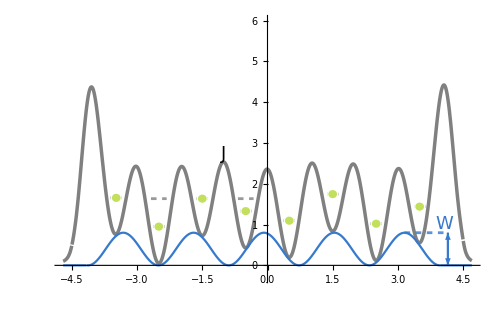
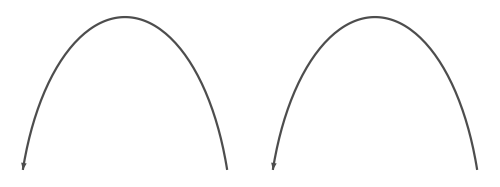

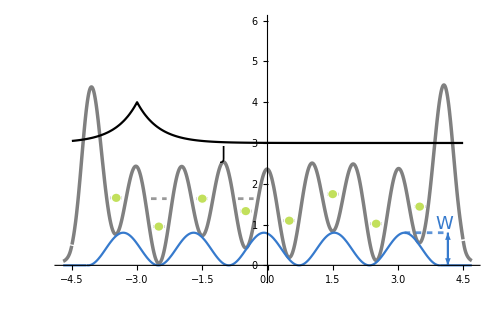
-Graphics-
-Graphics-

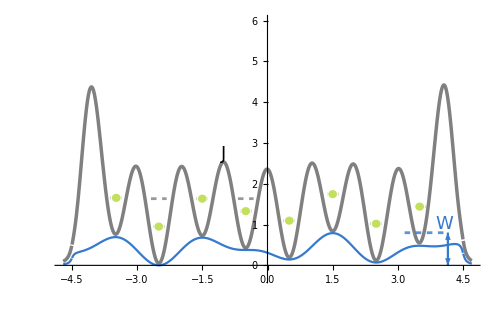
-Graphics-
-Graphics-

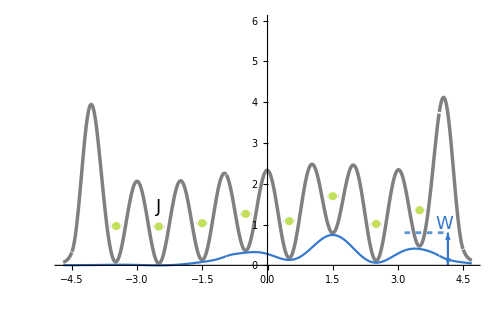
-Graphics-
-Graphics-

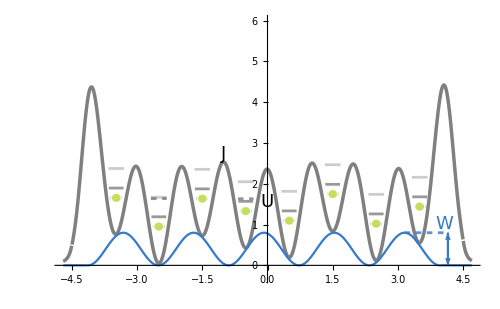
-Graphics-
-Graphics-

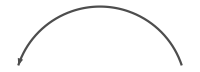
-Graphics-
-Graphics-

-Graphics-
-Graphics-

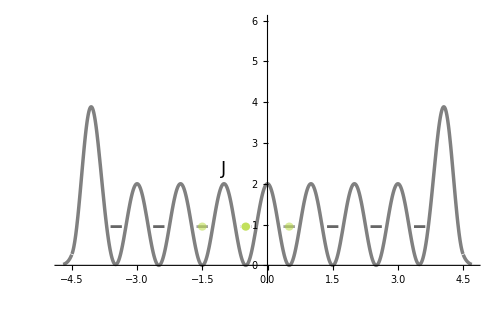
-Graphics-
-Graphics-

-Graphics-

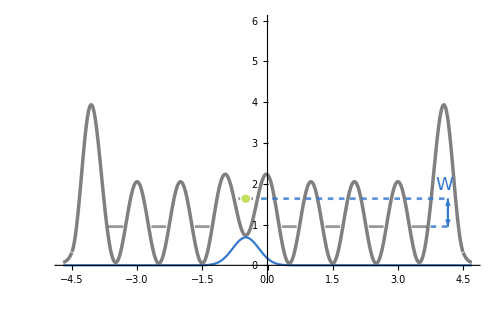

```mathematica
GR=(1+√5)/2;
Phi=0.16
WD=0.8
SmoothBox[x_,w_,dw_]:=1/π(ArcTan[(x+w)/dw]-ArcTan[(x-w)/dw])
DisordF[x_]:=WD*Cos[π x(GR-1)+Phi]^2 
DisordF1D[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x,4.5,0.05]
DisordF1DTherm[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x-1.5,2.45,0.25]
diskgreen= RGBColor[0.7, 0.85,0.2];

QPLC=ColorData[94,"ColorList"]⟦1⟧;
LW=0.13;
LW2=0.17;
LW3=0.18;
WlenR=4.15;
atomR=0.10;
atomShdwR=0.13;
Uo=0.15*0.8/0.5;
Ur=0.065;
FntSz=18;
LevelList=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,0.95+DisordF[-3.5]},{-3.48 + LW,0.95+DisordF[-3.5]}}],
Line[{{-2.5 - LW,0.95+DisordF[-2.5]},{-2.5+ LW,0.95+DisordF[-2.5]}}],
Line[{{-1.5- LW,0.95+DisordF[-1.5]},{-1.5+ LW,0.95+DisordF[-1.5]}}],
Line[{{-0.5 - LW,0.95+DisordF[-0.5]},{-0.5+ LW,0.95+DisordF[-0.5]}}],
Line[{{0.5 - LW,0.95+DisordF[0.5]},{0.5 + LW,0.95+DisordF[0.5]}}],Line[{{1.5- LW,0.95+DisordF[1.5]},{1.5 + LW,0.95+DisordF[1.5]}}],
Line[{{2.5- LW,0.95+DisordF[2.5]},{2.5+ LW,0.95+DisordF[2.5]}}],
Line[{{3.5 - LW,0.95+DisordF[3.5]},{3.5+ LW,0.95+DisordF[3.5]}}]
}];




LevelListTherm=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,0.95+DisordF1DTherm[-3.5]},{-3.48 + LW,0.95+DisordF1DTherm[-3.5]}}],
Line[{{-2.5 - LW,0.95+DisordF1DTherm[-2.5]},{-2.5+ LW,0.95+DisordF1DTherm[-2.5]}}],
Line[{{-1.5- LW,0.95+DisordF1DTherm[-1.5]},{-1.5+ LW,0.95+DisordF1DTherm[-1.5]}}],
Line[{{-0.5 - LW,0.95+DisordF1DTherm[-0.5]},{-0.5+ LW,0.95+DisordF1DTherm[-0.5]}}],
Line[{{0.5 - LW,0.95+DisordF1DTherm[0.5]},{0.5 + LW,0.95+DisordF1DTherm[0.5]}}],Line[{{1.5- LW,0.95+DisordF1DTherm[1.5]},{1.5 + LW,0.95+DisordF1DTherm[1.5]}}],
Line[{{2.5- LW,0.95+DisordF1DTherm[2.5]},{2.5+ LW,0.95+DisordF1DTherm[2.5]}}],
Line[{{3.5 - LW,0.95+DisordF1DTherm[3.5]},{3.5+ LW,0.95+DisordF1DTherm[3.5]}}]
}];

LevelList2=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.4],
Line[{{-3.48 - LW2,0.95+DisordF[-3.5]+Uo},{-3.48 + LW2,0.95+DisordF[-3.5]+Uo}}],
Line[{{-2.5 - LW2,0.95+DisordF[-2.5]+Uo},{-2.5+ LW2,0.95+DisordF[-2.5]+Uo}}],
Line[{{-1.5- LW2,0.95+DisordF[-1.5]+Uo},{-1.5+ LW2,0.95+DisordF[-1.5]+Uo}}],
Line[{{-0.5 - LW2,0.95+DisordF[-0.5]+Uo},{-0.5+ LW2,0.95+DisordF[-0.5]+Uo}}],
Line[{{0.5 - LW2,0.95+DisordF[0.5]+Uo},{0.5 + LW2,0.95+DisordF[0.5]+Uo}}],Line[{{1.5- LW2,0.95+DisordF[1.5]+Uo},{1.5 + LW2,0.95+DisordF[1.5]+Uo}}],
Line[{{2.5- LW2,0.95+DisordF[2.5]+Uo},{2.5+ LW2,0.95+DisordF[2.5]+Uo}}],
Line[{{3.5 - LW2,0.95+DisordF[3.5]+Uo},{3.5+ LW2,0.95+DisordF[3.5]+Uo}}]
}];

LevelList3=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.2],
Line[{{-3.48 - LW3,0.95+DisordF[-3.5]+3 Uo},{-3.48 + LW3,0.95+DisordF[-3.5]+3 Uo}}],
Line[{{-2.5 - LW3,0.95+DisordF[-2.5]+3 Uo},{-2.5+ LW3,0.95+DisordF[-2.5]+3 Uo}}],
Line[{{-1.5- LW3,0.95+DisordF[-1.5]+3 Uo},{-1.5+ LW3,0.95+DisordF[-1.5]+3 Uo}}],
Line[{{-0.5 - LW3,0.95+DisordF[-0.5]+3 Uo},{-0.5+ LW3,0.95+DisordF[-0.5]+3 Uo}}],
Line[{{0.5 - LW3,0.95+DisordF[0.5]+3 Uo},{0.5 + LW3,0.95+DisordF[0.5]+3 Uo}}],Line[{{1.5- LW3,0.95+DisordF[1.5]+3 Uo},{1.5 + LW3,0.95+DisordF[1.5]+3 Uo}}],
Line[{{2.5- LW3,0.95+DisordF[2.5]+3 Uo},{2.5+ LW3,0.95+DisordF[2.5]+3 Uo}}],
Line[{{3.5 - LW3,0.95+DisordF[3.5]+3 Uo},{3.5+ LW3,0.95+DisordF[3.5]+3 Uo}}]
}];

WLevels = Graphics[{Thickness[0.004],
QPLC,
Opacity[0.8],
Dashing[0.008],
Line[{{(2 π-Phi)/(π (GR-1)),WD},{WlenR,WD}}]
}];
WLevelsFlatOffset= Graphics[{Thickness[0.004],
QPLC,
Opacity[0.8],
Dashing[0.008],
Line[{{(2 π-Phi)/(π (GR-1))-3.3,DisordF[-1.5]+0.95},{WlenR,DisordF[-1.5]+0.95}}],
Line[{{(2 π-Phi)/(π (GR-1))+0.6,0.95},{WlenR,0.95}}]
}];


DLevels= Graphics[{Thickness[0.004],
RGBColor["Black"],
Opacity[0.4],
Dashing[0.008],
Line[{{-0.5- LW3,0.95+DisordF[-1.5]},{-0.5+ LW3,0.95+DisordF[-1.5]}}],
Line[{{-2.5 - LW3,0.95+DisordF[-1.5]},{-2.5+ LW3,0.95+DisordF[-1.5]}}]
}];

DLevelsTherm= Graphics[{Thickness[0.004],
RGBColor["Black"],
Opacity[0.4],
Dashing[0.008],
Line[{{-3.5- LW3,0.95+DisordF1DTherm[-2.5]},{-3.5+ LW3,0.95+DisordF1DTherm[-1.5]}}],
Line[{{-1.5 - LW3,0.95+DisordF1DTherm[-2.5]},{-1.5+ LW3,0.95+DisordF1DTherm[-1.5]}}]
}];


AtomList=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomR,atomR}]}];
AtomListShadow=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-3.48,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomShdwR,atomShdwR}]}];

AtomListTherm=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-3.48,0.95+DisordF1DTherm[-3.5]},{atomR,atomR}],
Disk[{-2.5,0.95+DisordF1DTherm[-2.5]},{atomR,atomR}],
Disk[{-1.5,0.95+DisordF1DTherm[-1.5]},{atomR,atomR}],
Disk[{-0.5,0.95+DisordF1DTherm[-0.5]},{atomR,atomR}],
Disk[{0.5,0.95+DisordF1DTherm[0.5]},{atomR,atomR}],
Disk[{1.5,0.95+DisordF1DTherm[1.5]},{atomR,atomR}],
Disk[{2.5,0.95+DisordF1DTherm[2.5]},{atomR,atomR}],
Disk[{3.5,0.95+DisordF1DTherm[3.5]},{atomR,atomR}]}];


AtomListShadowTherm=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-3.48,0.95+DisordF1DTherm[-3.5]},{atomShdwR,atomShdwR}],
Disk[{-2.5,0.95+DisordF1DTherm[-2.5]},{atomShdwR,atomShdwR}],
Disk[{-1.5,0.95+DisordF1DTherm[-1.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5,0.95+DisordF1DTherm[-0.5]},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95+DisordF1DTherm[0.5]},{atomShdwR,atomShdwR}],
Disk[{1.5,0.95+DisordF1DTherm[1.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,0.95+DisordF1DTherm[2.5]},{atomShdwR,atomShdwR}],
Disk[{3.5,0.95+DisordF1DTherm[3.5]},{atomShdwR,atomShdwR}]}];




LevelListFlat=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,0.95},{-3.48 + LW,0.95}}],
Line[{{-2.5 - LW,0.95},{-2.5+ LW,0.95}}],
Line[{{-1.5- LW,0.95},{-1.5+ LW,0.95}}],
Line[{{-0.5 - LW,0.95},{-0.5+ LW,0.95}}],
Line[{{0.5 - LW,0.95},{0.5 + LW,0.95}}],
Line[{{1.5- LW,0.95},{1.5 + LW,0.95}}],
Line[{{2.5- LW,0.95},{2.5+ LW,0.95}}],
Line[{{3.5 - LW,0.95},{3.5+ LW,0.95}}]
}];
LevelListFlat2=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.4],
Line[{{-3.5 - LW2+0.01,0.95 + Uo},{-3.5+ LW2+0.01,0.95 + Uo}}],
Line[{{-2.5 - LW2,0.95 + Uo},{-2.5+ LW2,0.95 + Uo}}],
Line[{{-1.5 - LW2,0.95 + Uo},{-1.5+ LW2,0.95 + Uo}}],
Line[{{-0.5 - LW2,0.95 + Uo},{-0.5+ LW2,0.95 + Uo}}],
Line[{{0.5 - LW2,0.95 + Uo},{0.5+ LW2,0.95 + Uo}}],
Line[{{1.5 - LW2,0.95 + Uo},{1.5+ LW2,0.95 + Uo}}],
Line[{{2.5 - LW2,0.95 + Uo},{2.5+ LW2,0.95 + Uo}}],
Line[{{3.5 - LW2-0.01,0.95 + Uo},{3.5+ LW2-0.01,0.95 + Uo}}]
}];


LevelListFlatOffset=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.4],
Line[{{-3.5 - LW2+0.01,0.95 },{-3.5+ LW2+0.01,0.95 }}],
Line[{{-2.5 - LW2,0.95 },{-2.5+ LW2,0.95 }}],
Line[{{-1.5 - LW2,0.95},{-1.5+ LW2,0.95 }}],
Line[{{-0.5 - LW2,0.95+DisordF[-1.5] },{-0.5+ LW2,0.95+DisordF[-1.5] }}],
Line[{{0.5 - LW2,0.95},{0.5+ LW2,0.95 }}],
Line[{{1.5 - LW2,0.95},{1.5+ LW2,0.95 }}],
Line[{{2.5 - LW2,0.95 },{2.5+ LW2,0.95}}],
Line[{{3.5 - LW2-0.01,0.95},{3.5+ LW2-0.01,0.95}}]
}];


AtomListShadowFlat=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-0.5,0.95},{atomShdwR,atomShdwR}]
}];
AtomListFlat=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-0.5,0.95},{atomR,atomR}]
}];
AtomListShadowFlatU=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-0.5,0.95+Uo},{atomShdwR,atomShdwR}]
}];
AtomListFlatU1=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-0.5+Ur Cos[2 π /3+π/6],0.95+Uo+Ur Sin[2 π /3+π/6]},{atomR,atomR}]
}];
AtomListShadowFlatU1=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-0.5+Ur Cos[2 π /3+π/6],0.95+Uo+Ur Sin[2 π /3+π/6]},{atomShdwR,atomShdwR}]
}];
AtomListFlatU2=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-0.5+Ur Cos[5 π /3+π/6],0.95+ Uo+Ur Sin[5 π /3+π/6]},{atomR,atomR}]
}];
AtomListShadowFlatU2=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-0.5+Ur Cos[5 π /3+π/6],0.95+ Uo+Ur Sin[5 π /3+π/6]},{atomShdwR,atomShdwR}]
}];

AtomListShadowFlat2=Graphics[{ 
RGBColor["White"],
Opacity[0.4],
Disk[{-1.5,0.95},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95},{atomShdwR,atomShdwR}]
}];
AtomListFlat2=Graphics[{ 
diskgreen,
Opacity[0.5],
Disk[{-1.5,0.95},{atomR,atomR}],
Disk[{0.5,0.95},{atomR,atomR}]
}];
rdsAndAnglsFlat={{0.05,{0.1 π,π 0.9}}};
arcsHopFlat= Graphics[{
Inset[arcsWArrows[rdsAndAnglsFlat],{-1,1.2}],
Inset[arcsWArrows[rdsAndAnglsFlat],{0,1.2}]
}];
labelsFlat={Graphics[{
{Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-1,2.15},{0,-1}]}
}]};
labelsFlatU={Graphics[{
{Text[Style[ToExpression["U",TeXForm,HoldForm],FntSz],{-1,1},{0,-1}]}
}]};
labelsFlatD={Graphics[{
{QPLC,Text[Style[ToExpression["W",TeXForm,HoldForm],FntSz],{4.075,0.8+0.95},{0,-1}]}
}]};
AtomListShadowFlatUD=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-0.5,0.95+DisordF[-1.5]},{atomShdwR,atomShdwR}]
}];
AtomListFlatUD=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-0.5,0.95+DisordF[-1.5]},{atomR,atomR}]
}];





AtomListShadow2a=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-3.48,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5-0.04,0.95+DisordF[-0.5]+Uo+0.03},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomShdwR,atomShdwR}]}];
AtomListShadow2b=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-0.5+0.04,0.95+DisordF[-0.5]+Uo-0.03},{atomShdwR,atomShdwR}],
}];

AtomList2a=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}],
Disk[{-0.5-0.04,0.95+DisordF[-0.5]+Uo+0.03},{atomR,atomR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomR,atomR}]}];

AtomList2b=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-0.5+0.04,0.95+DisordF[-0.5]+Uo-0.03},{atomR,atomR}]}];


AtomList2c=Graphics[{
Opacity[0.8],
Thickness[0.004],
Dashed,
Circle[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}],
Circle[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}]}];
AtomListShadow2c=Graphics[{ 
RGBColor["White"],
Opacity[1],
Thickness[0.005],
Circle[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}],
Circle[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}]
}];

AtomList2d=Graphics[{
diskgreen,
Opacity[0.55],
EdgeForm[Dashing[0.005]],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}]}];

AtomListShadow2d=Graphics[{ 
RGBColor["White"],
Opacity[0.4],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}]
}];

AtomList2e=Graphics[{
diskgreen,
Opacity[0.55],
EdgeForm[Dashing[0.005]],
Disk[{-3.5,0.95+DisordF[-3.5]},{atomR,atomR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}]
}];
AtomList2f1=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-2.5+Ur Cos[2 π /3+π/6],0.95+DisordF[-2.5]+3 Uo+Ur Sin[2 π /3+π/6]},{atomR,atomR}]
}];
AtomList2f2=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-2.5+Ur Cos[ 2 2 π /3+π/6],0.95+DisordF[-2.5]+3 Uo+Ur Sin[2 2 π /3+π/6]},{atomR,atomR}]
}];
AtomList2f3=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-2.5+Ur Cos[3 2 π /3+π/6],0.95+DisordF[-2.5]+3 Uo+Ur Sin[3 2 π /3+π/6]},{atomR,atomR}]
}];


AtomListShadow2f1=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-2.5+Ur Cos[2 π /3+π/6],0.95+DisordF[-2.5]+3 Uo+Ur Sin[2 π /3+π/6]},{atomShdwR,atomShdwR}]
}];
AtomListShadow2f2=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-2.5+Ur Cos[2 2 π /3+π/6],0.95+DisordF[-2.5]+3 Uo+Ur Sin[2 2 π /3+π/6]},{atomShdwR,atomShdwR}]
}];
AtomListShadow2f3=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-2.5+Ur Cos[3 2 π /3+π/6],0.95+DisordF[-2.5]+3 Uo+Ur Sin[3 2 π /3+π/6]},{atomShdwR,atomShdwR}]
}];


AtomListShadow3a=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomShdwR,atomShdwR}]}];

AtomList3a=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomR,atomR}]}];


USpikeBall=Graphics[{GenerateSpikeBall[{-0.5,0.95+DisordF[-0.5]+Uo},0.52,0.85]}];
USpikeBall=Graphics[{SpikeBallRed,Opacity[0.52],EdgeForm[{Thickness[0.000001],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-0.5,0.95+DisordF[-0.5]+Uo},0.52,0.75]}}];
USpikeBall3U=Graphics[{SpikeBallRed,Opacity[0.52],EdgeForm[{Thickness[0.000001],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-2.5,0.95+DisordF[-2.5]+3 Uo},0.52,0.75]}}];
USpikeBallFlat= Graphics[{SpikeBallRed,Opacity[0.52],EdgeForm[{Thickness[0.000001],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-0.5,0.95+Uo},0.57,0.75]}}];

UArrow=Graphics[{
Arrow[{{0,0.2+0.95+DisordF[0.5]},{0,0+0.95+DisordF[0.5]}}],
Arrow[{{0,0+0.95+DisordF[0.5]},{0,0.2+0.95+DisordF[0.5]}}]
}
];
WArrows=Graphics[{Thickness[0.003],
QPLC,
{Arrowheads[0.022],Arrow[{{WlenR,0},{WlenR,WD}}]},
{Arrowheads[0.022],Arrow[{{WlenR,WD},{WlenR,0}}]}
}];

WArrowsFlatOffset=Graphics[{Thickness[0.003],
QPLC,
{Arrowheads[0.022],Arrow[{{WlenR,0+0.95},{WlenR,DisordF[-1.5]+0.95}}]},
{Arrowheads[0.022],Arrow[{{WlenR,DisordF[-1.5]+0.95},{WlenR,0+0.95}}]}
}];

rdsAndAngls={{0.075,{0.1 π,π 0.9}}};

arcsWArrows[rdsAndAngls];
arcs=Graphics[{
Inset[arcsWArrows[rdsAndAngls],{3,1.6}],
Inset[arcsWArrows[rdsAndAngls],{2,1.6}],
Inset[arcsWArrows[rdsAndAngls],{1,1.6}],
Inset[arcsWArrows[rdsAndAngls],{0,1.6}],
Inset[arcsWArrows[rdsAndAngls],{-1,1.6}],
Inset[arcsWArrows[rdsAndAngls],{-2,1.6}],
Inset[arcsWArrows[rdsAndAngls],{-3,1.6}]
}];
arcsSS=Graphics[{
Inset[arcsWArrows[rdsAndAngls],{-2,DisordF[1.5]+1.2}],
Inset[arcsWArrows[rdsAndAngls],{-1,DisordF[1.5]+1.2}]
}];
arcsSSTherm=Graphics[{
Inset[arcsWArrows[rdsAndAngls],{-3,DisordF[-2.5]+1.2}],
Inset[arcsWArrows[rdsAndAngls],{-2,DisordF[-2.5]+1.2}]
}];
arcsHop = Graphics[{
Inset[arcsWArrows[rdsAndAngls],{-1,DisordF[-1.5]+1.2}]
}];


arcsHop2 = Graphics[{
Inset[arcsWArrows[rdsAndAngls],{-3,DisordF[-2.5]+1.2+3Uo}],
Inset[arcsWArrows[rdsAndAngls],{-2,DisordF[-2.5]+1.2+3Uo}]
}];

labelsa={Graphics[{
{Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-1,2.5},{0,-1}]},
{QPLC,Text[Style[ToExpression["W",TeXForm,HoldForm],FntSz],{4.075,0.8},{0,-1}]}
}]};
labelsb={Graphics[{
{Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-1,2.5},{0,-1}]},
{Text[Style[ToExpression["U",TeXForm,HoldForm],FntSz],{0,DisordF[-0.5]+0.95},{0,-1}]},
{QPLC,Text[Style[ToExpression["W",TeXForm,HoldForm],FntSz],{4.075,0.8},{0,-1}]}
}]};

labelsbb={Graphics[{
{Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-1,2.5},{0,-1}]},
{SpikeBallRed,Opacity[0.8],Text[Style[ToExpression["U",TeXForm,HoldForm],FntSz],{0,DisordF[-0.5]+0.95},{0,-1}]},
{QPLC,Text[Style[ToExpression["W",TeXForm,HoldForm],FntSz],{4.075,0.8},{0,-1}]}
}]};


labelsc={Graphics[{
{Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-2,2.5},{0,-1}]},
{SpikeBallRed,Opacity[0.8],Text[Style[ToExpression["U",TeXForm,HoldForm],FntSz],{-2,1},{0,-1}]},
{QPLC,Text[Style[ToExpression["W",TeXForm,HoldForm],FntSz],{4.075,0.8},{0,-1}]}
}]};

labelsTherm={Graphics[{
{Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-2.5,1.2},{0,-1}]},
{QPLC,Text[Style[ToExpression["W",TeXForm,HoldForm],FntSz],{4.075,0.8},{0,-1}]}
}]};

barelatt=Plot[{Gauss[x,-4.1,0.2]+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]+ (DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.2 1.6 + 2 1.6),1,0])},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];
barelattV2=Plot[{Gauss[x,-4.1,0.2]+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]+ DisordF1D[x]+0.05},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

barelattV3Therm=Plot[{Gauss[x,-4.1,0.2]+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]+ DisordF1DTherm[x]+0.05},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];
barelattVFlat=Plot[{Gauss[x,-4.1,0.2]+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

GQP1=Plot[ (DisordF[-3.5]) Gauss[x,-3.5,0.1]/Gauss[-3.5,-3.5,0.1] ,
{x,-5,-3},
PlotStyle-> {{RGBColor["Black"],Dashed}},
PlotRange-> {{-4.7,4.7},{-0.3,6}}];
GQP2=Plot[ (DisordF[-2.5]) Gauss[x,-2.5,0.1]/Gauss[-3.5,-3.5,0.1] ,
{x,-3,-2},
PlotStyle-> {{RGBColor["Black"],Dashed}},
PlotRange-> {{-4.7,4.7},{-0.3,6}}];
GQP3=Plot[ (DisordF[-1.5]) Gauss[x,-1.5,0.1]/Gauss[-3.5,-3.5,0.1] ,
{x,-2,-1},
PlotStyle-> {{RGBColor["Black"],Dashed}},
PlotRange-> {{-4.7,4.7},{-0.3,6}}];
GQP4=Plot[ (DisordF[-0.5]) Gauss[x,-0.5,0.1]/Gauss[-3.5,-3.5,0.1] ,
{x,-1,0},
PlotStyle-> {{RGBColor["Black"],Dashed}},
PlotRange-> {{-4.7,4.7},{-0.3,6}}];
GQP5=Plot[ (DisordF[3.5]) Gauss[x,3.5,0.1]/Gauss[-3.5,-3.5,0.1] ,
{x,3,5},
PlotStyle-> {{RGBColor["Black"],Dashed}},
PlotRange-> {{-4.7,4.7},{-0.3,6}}];
GQP6=Plot[ (DisordF[2.5]) Gauss[x,2.5,0.1]/Gauss[-3.5,-3.5,0.1] ,
{x,2,3},
PlotStyle-> {{RGBColor["Black"],Dashed}},
PlotRange-> {{-4.7,4.7},{-0.3,6}}];
GQP7=Plot[ (DisordF[1.5]) Gauss[x,1.5,0.1]/Gauss[-3.5,-3.5,0.1] ,
{x,1,2},
PlotStyle-> {{RGBColor["Black"],Dashed}},
PlotRange-> {{-4.7,4.7},{-0.3,6}}];
GQP8=Plot[ (DisordF[0.5]) Gauss[x,0.5,0.1]/Gauss[-3.5,-3.5,0.1] ,
{x,0,1},
PlotStyle-> {{RGBColor["Black"],Dashed}},
PlotRange-> {{-4.7,4.7},{-0.3,6}}];




barelattVoffset=Plot[{Gauss[x,-4.1,0.2]+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]+ 0.05+
(Gauss[x,-0.5,0.3]/Gauss[-0.5,-0.5,0.3]) DisordF[-1.5]},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

OffsetV=Plot[
(Gauss[x,-0.5,0.3]/Gauss[-0.5,-0.5,0.3]) DisordF[-1.5],
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
AxesStyle-> Opacity[0],
PlotStyle-> {{QPLC}}
];


OffsetVFrame=Plot[
(Gauss[x,-0.5,0.3]/Gauss[-0.5,-0.5,0.3]) DisordF[-1.5],
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
AxesStyle-> Opacity[0],
PlotStyle-> {Opacity[0]}
];
(* (Gauss[x,-0.75,0.3]/Gauss[-0.75,-0.75,0.3]+Gauss[x,-0.25,0.3]/Gauss[-0.25,-0.25,0.3])/3*)



QP=Plot[{(DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-4.7,4.7},
AxesStyle-> Opacity[0],
PlotStyle-> {{QPLC}}];
QP2=Plot[{(DisordF1D[x])},
{x,-4.7,4.7},
AxesStyle-> Opacity[0],
PlotStyle-> {{QPLC}}];

QP3=Plot[{(DisordF1DTherm[x])},
{x,-4.7,4.7},
AxesStyle-> Opacity[0],
PlotStyle-> {{QPLC}}];


AL=Show[barelattV2,
LevelList,WLevels,DLevels,
AtomList2d,arcsSS,WArrows,
(*GQP1,GQP2,GQP3,GQP4,GQP5,GQP6,GQP7,GQP8,*)
QP,
(*AtomListShadow,AtomList,*)
AtomListShadow,AtomList,
labelsa]
(*Export["AL.pdf",%,Rasterize-> False]*)
(*Export["AL.png",%,Rasterize-> False,ImageResolution-> 1000]*)

AL2=Show[barelattV2,
LevelList,WLevels,DLevels,
AtomList2d,arcsSS,WArrows,
(*GQP1,GQP2,GQP3,GQP4,GQP5,GQP6,GQP7,GQP8,*)
QP,
(*AtomListShadow,AtomList,*)
AtomListShadow,AtomList,
labelsa,
EXPPlot]
(*Export["MBL_EXP.pdf",%,Rasterize-> False,ImageResolution-> 2000]*)

(*Export["AL.pdf",%,Rasterize-> False]*)
(*Export["AL.png",%,Rasterize-> False,ImageResolution-> 1000]*)

ALRealLatt=Show[barelattV2,
LevelList,WLevels,DLevels,
AtomList2d,arcsSS,WArrows,
(*GQP1,GQP2,GQP3,GQP4,GQP5,GQP6,GQP7,GQP8,*)
QP2,
(*AtomListShadow,AtomList,*)
AtomListShadow,AtomList,
labelsa]
(*Export["ALReal.pdf",%,Rasterize-> False]*)
(*Export["ALReal.png",%,Rasterize-> False,ImageResolution-> 1000]*)
ThermReg=Show[barelattV3Therm,
QP3,
WLevels,
WArrows,
LevelListTherm,
AtomListShadowTherm,
AtomListTherm,
labelsTherm,
arcsSSTherm
]
(*Export["MBL_Therm.png",%,Rasterize-> False,ImageResolution-> 1000]*)



LOCP=Show[barelattV2,
LevelList,WLevels,DLevels,LevelList2,LevelList3,
AtomList2d,arcsSS,WArrows,
(*GQP1,GQP2,GQP3,GQP4,GQP5,GQP6,GQP7,GQP8,*)
QP,
(*AtomListShadow,AtomList,*)
AtomListShadow,AtomList,
labelsb]
(*Export["LOCP.pdf",%,Rasterize-> False]*)

(*Export["LOCP.pdf",%,Rasterize-> False,ImageResolution-> 2000]*)

MBL=Show[barelattV2,
AtomList2d,
LevelList,LevelList2,LevelList3,WLevels,
arcsHop,WArrows,
(*GQP1,GQP2,GQP3,GQP4,GQP5,GQP6,GQP7,GQP8,*)
QP,
(*AtomListShadow,AtomList,*)
USpikeBall,
AtomListShadow2b,AtomList2b,
AtomListShadow2a,AtomList2a,
labelsbb]
(*Export["MBL.pdf",%,Rasterize-> False]*)

(*Export["MBL.pdf",%,Rasterize-> False,ImageResolution-> 1000]*)


MBL2=Show[barelattV2,
LevelList,LevelList2,LevelList3,WLevels,
arcsHop2,WArrows,
(*GQP1,GQP2,GQP3,GQP4,GQP5,GQP6,GQP7,GQP8,*)
QP,
(*AtomListShadow,AtomList,*)
USpikeBall3U,
AtomListShadow3a,AtomList3a,
AtomList2e,
AtomListShadow2f1,AtomList2f1,
AtomListShadow2f2,AtomList2f2,
AtomListShadow2f3,AtomList2f3,
labelsc
]

(*Export["MBL2.pdf",%,Rasterize-> False,ImageResolution-> 2000]*)

FlatLatt=Show[
OffsetVFrame,
LevelListFlat,
barelattVFlat,
arcsHopFlat,
labelsFlat,
AtomListShadowFlat,
AtomListFlat,
AtomListShadowFlat2,
AtomListFlat2
]

(*Export["MBL_BHJ.pdf",%,Rasterize-> False,ImageResolution-> 2000]*)

FlatLattU=Show[
OffsetVFrame,
LevelListFlat,
LevelListFlat2,
barelattVFlat,
labelsFlatU,
USpikeBallFlat,
AtomListShadowFlatU1,
AtomListFlatU1,
AtomListShadowFlatU2,
AtomListFlatU2
]

(*Export["MBL_BHU.pdf",%,Rasterize-> False,ImageResolution-> 2000]*)

FlatLattD=Show[
OffsetVFrame,
barelattVoffset,
LevelListFlatOffset,
labelsFlatD,
AtomListShadowFlatUD,
AtomListFlatUD,
WArrowsFlatOffset,
OffsetV,
WLevelsFlatOffset
]

(*Export["MBL_BHD.pdf",%,Rasterize-> False,ImageResolution-> 2000]*)
```

```mathematica
f
```

f

```mathematica
USpikeBall=Graphics[{SpikeBallRed,Opacity[0.52],EdgeForm[{Thickness[0.000001],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-0.5,0.95+DisordF[-0.5]+Uo},0.52,0.75]}}];
MBL=Show[barelattV2,
AtomList2d,
LevelList,LevelList2,LevelList3,WLevels,
arcsHop,WArrows,
(*GQP1,GQP2,GQP3,GQP4,GQP5,GQP6,GQP7,GQP8,*)
QP,
(*AtomListShadow,AtomList,*)
USpikeBall,
AtomListShadow2b,AtomList2b,
AtomListShadow2a,AtomList2a,
labelsb]
SpikeBallRed=ColorData[93,"ColorList"]⟦1⟧
```

-Graphics-
-Graphics-

Hue[0, 0.8, 0.85]

```mathematica
ColorData[88,"ColorList"]
ColorData[89,"ColorList"]
{{ColorData[90,"ColorList"]}, {ColorData[91,"ColorList"]}}
ColorData[92,"ColorList"]
ColorData[93,"ColorList"]
ColorData[94,"ColorList"]
ColorData[95,"ColorList"]
ColorData[96,"ColorList"]
ColorData[97,"ColorList"]
```

{Hue[0.42, 0.67, 0.75],Hue[0.17, 1, 0.75],Hue[0.05, 0.7, 1],Hue[0.5, 0.67, 0.75],Hue[0.67, 0.5, 1],Hue[0.08, 1, 1],Hue[0.25, 0.67, 0.75],Hue[0.11, 0.75, 1],Hue[0.33, 0.33, 0.75],Hue[0.11, 1, 0.9]}

{Hue[0.5, 0.5, 0.4],Hue[0.08, 0.9, 0.8],Hue[0.42, 0.67, 0.6],Hue[0.13, 0.8, 0.85],Hue[0.5, 0.67, 0.6],Hue[0.17, 0.9, 0.6],Hue[0.67, 0.5, 0.7],Hue[0.1, 0.75, 0.8],Hue[0, 0.75, 0.8],Hue[0.04, 0.8, 1]}

{{{Hue[0.22, 1, 0.6],Hue[0.01, 0.8, 0.8],Hue[0.61, 0.75, 1],Hue[0.11, 1, 0.75],Hue[0.67, 0.6, 0.9],Hue[0.17, 1, 0.5],Hue[0.06, 1, 0.75],Hue[0.8, 0.5, 0.6],Hue[0.25, 1, 0.5],Hue[0.58, 0.67, 0.75]}},{{Hue[0.58, 0.67, 0.66],Hue[0.17, 1, 0.66],Hue[0.45, 0.75, 0.6],Hue[0.12, 0.7, 0.7],Hue[0.25, 0.7, 0.6],Hue[0.58, 0.5, 0.8],Hue[0.11, 1, 0.66],Hue[0.06, 0.75, 0.88],Hue[0.5, 0.5, 0.44],Hue[0.67, 0.33, 0.66]}}}

{Hue[0.12, 1, 0.9],Hue[0.08, 1, 0.7],Hue[0.08, 1, 0.92],Hue[0.17, 1, 0.5],Hue[0.12, 0.7, 0.8],Hue[0, 0.33, 0.6],Hue[0.11, 1, 0.8],Hue[0.5, 0.5, 0.5],Hue[0.17, 1, 0.7],Hue[0.06, 1, 0.69]}

{Hue[0, 0.8, 0.85],Hue[0.11, 0.75, 0.92],Hue[0.17, 0.6, 0.52],Hue[0.06, 0.75, 0.92],Hue[0.5, 0.5, 0.55],Hue[0.17, 0.67, 0.69],Hue[0.67, 0.33, 0.69],Hue[0.5, 0.33, 0.69],Hue[0.94, 0.5, 0.69],Hue[0.25, 0.6, 0.7]}

{RGBColor[0.21020243862087418, 0.47802869583858715, 0.802198107305176],RGBColor[0.7072726887298498, 0.36734389310000776, 0.22572660836392477],RGBColor[0., 0.5478609782372904, 0.4891696614045123],RGBColor[0.6451793884320347, 0.3592839366958893, 0.6737368466913262],RGBColor[0.4795214457262614, 0.4794496852752767, 0.08944520674023174],RGBColor[0., 0.5239638039480364, 0.7467101989958554],RGBColor[0.7618211845684226, 0.3099312712025551, 0.39120711213803705],RGBColor[0., 0.5380756485327808, 0.3011937398484862],RGBColor[0.4306391086785686, 0.4367088653451986, 0.7829127834334554],RGBColor[0.636471896284624, 0.413870747850409, 0.1431778775285077],RGBColor[0., 0.545007293737855, 0.6028975638566113],RGBColor[0.722244276284985, 0.31998937783312603, 0.5726766768035847],RGBColor[0.35984212281381656, 0.5088638151315594, 0.14452408433947048],RGBColor[0., 0.4987546431531366, 0.7933744520922773],RGBColor[0.7379047109639936, 0.34055347063409547, 0.2850977041876611]}

{RGBColor[0.5477407734491414, 0.6781411651751702, 0.9198755683649779],RGBColor[0.87058837853668, 0.6048248459110492, 0.4922838688297661],RGBColor[0.31573973298228514, 0.7398396909727576, 0.6872935044932373],RGBColor[0.8116530610702385, 0.6012280787481186, 0.8258505440142531],RGBColor[0.6930177876644076, 0.6799721277526325, 0.4199343626084721],RGBColor[0.3657383773643357, 0.7160575963243984, 0.8785934977977451],RGBColor[0.9085681481061203, 0.5752950706176673, 0.6133049627289092],RGBColor[0.45090413446768524, 0.7307307156470545, 0.5496494250722427],RGBColor[0.6615631128722788, 0.6485376038586634, 0.9060767343018842],RGBColor[0.8161522125541179, 0.6330873483332724, 0.44162556936219965],RGBColor[0.2788463407977611, 0.7364662593350805, 0.7719277055909679],RGBColor[0.872285951379566, 0.5806850315835889, 0.7504553721898173],RGBColor[0.6034618967403447, 0.7041963165762994, 0.44827550563732105],RGBColor[0.475063788418671, 0.6944493828400345, 0.9131877670467264],RGBColor[0.8931418160634189, 0.5902914113092578, 0.534183346558588]}

{RGBColor[0.23792049598428056, 0.6887478786077664, 1.],RGBColor[1., 0.519591857134656, 0.3096724501821112],RGBColor[0., 0.7904150911428401, 0.7051174286912738],RGBColor[0.9363550506359628, 0.5065315445234129, 0.9811070357073114],RGBColor[0.686958812227552, 0.6905735387590792, 0.05772651708573071],RGBColor[0., 0.7563606470844539, 1.],RGBColor[1., 0.42721725970620367, 0.5588721269654955],RGBColor[0., 0.7762699669879868, 0.4226781993994135],RGBColor[0.6109120054767144, 0.6265300918182286, 1.],RGBColor[0.9205702487735915, 0.5917459414248752, 0.1760364705511712],RGBColor[0., 0.7864948250314334, 0.8753587584942155],RGBColor[1., 0.4434532437298291, 0.8298247530580691],RGBColor[0.5070558429142891, 0.7339027322149217, 0.17362470759792137],RGBColor[0., 0.7194858914960536, 1.],RGBColor[1., 0.4770567658488352, 0.3999994395810451]}

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
SpikeBallRed=ColorData[93,"ColorList"]⟦1⟧
```

Hue[0, 0.8, 0.85]

```mathematica
Plot[{DisordF[x],DisordF1D[x]},{x,-4,4}];
```

```mathematica
SmoothBox[x_,w_,dw_]:=1/π(ArcTan[(x+w)/dw]-ArcTan[(x-w)/dw])
DisordF[x_]:=WD*Cos[π x(GR-1)+Phi]^2 
DisordF1D[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)
Plot[{DisordF[x]+5 Cos[x π ]^2,DisordF1D[x] SmoothBox[x,3.95,0.1]+5 Cos[x π ]^2,DisordF1D[x] SmoothBox[x,3.95,0.1]},{x,-10,10}];
```

```mathematica
Graphics[{GenerateSpikeBall[{0,0},0.55,0.85],GenerateSpikeBall[{2,0},0.75,0.25],GenerateSpikeBall[{4,0},0.75,0.1]}]
```

-Graphics-

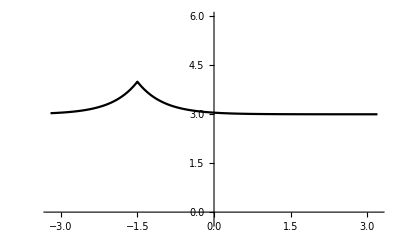

```mathematica
EXPPlot=Plot[
Exp[-Abs[x+1.5]/0.5]+3,
{x,-3.2,3.2},
PlotRange-> {{-3.2,3.2},{-0.3,6}},
PlotStyle-> {RGBColor[{0,0,0}]},
AxesStyle-> Opacity[0]
]
```

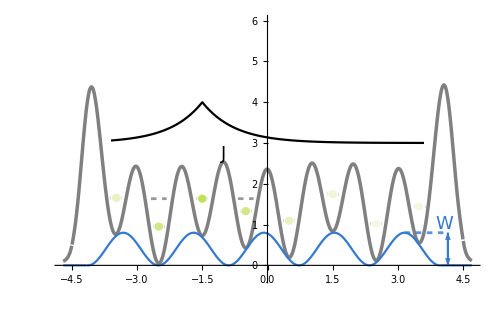
-Graphics-
-Graphics-

```mathematica
EXPPlot=Plot[
Exp[-Abs[x+1.5]/0.75]+3,
{x,-3.6,3.6},
PlotRange-> {{-3.6,3.6},{-0.3,6}},
PlotStyle-> {RGBColor[{0,0,0}]},
AxesStyle-> Opacity[0]
];
AtomListAL=Graphics[{ 
diskgreen,
{Opacity[0.3],Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}]},
{Opacity[0.6],Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}]},
{Opacity[0.6],Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}]},
{Opacity[0.3],Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}]},
{Opacity[0.2],Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}]},
{Opacity[0.15],Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}]},
{Opacity[0.15],Disk[{3.48,0.95+DisordF[3.5]},{atomR,atomR}]}
}];

AtomListShadowAL=Graphics[{ 
RGBColor["White"],
{Opacity[1],Disk[{-3.48,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-1.5,0.95+DisordF[-1.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{3.5,0.95+DisordF[3.5]},{atomShdwR,atomShdwR}]}
}];

AtomListShadow;
AtomList;
AL2=Show[barelattV2,
LevelList,WLevels,DLevels,arcsSS,WArrows,
(*GQP1,GQP2,GQP3,GQP4,GQP5,GQP6,GQP7,GQP8,*)
QP,
(*AtomListShadow,AtomList,*)
AtomListShadowAL,AtomListAL,
labelsa,
EXPPlot]
(*Export["MBL_BH_EXP_LBIT.pdf",%,Rasterize-> False,ImageResolution-> 2000]*)
```

```mathematica
EXPPlot2=Plot[
Exp[-Abs[x-0.5]/0.75]+3,
{x,-3.6,3.6},
PlotRange-> {{-3.6,3.6},{-0.3,6}},
PlotStyle-> {RGBColor[{0,0,0}]},
Axes-> False
];
EXPPlotCB2=Plot[
{Exp[-Abs[x+1.5]/0.75]+3},
{x,-0.5,3.6},
PlotRange-> {{-3.6,-0.5},{-0.3,6}},
PlotStyle-> {Opacity[0],RGBColor[{0,0,0}]},
Axes-> False,
Filling->3,
FillingStyle-> Directive[Opacity[0.52],SpikeBallRed]
];
EXPPlotCB1=Plot[
{Exp[-Abs[x-0.5]/0.75]+3},
{x,-3.6,-0.5},
PlotRange-> {{-3.6,-0.5},{-0.3,6}},
PlotStyle-> {Opacity[0],RGBColor[{0,0,0}]},
Axes-> False,
Filling->3,
FillingStyle-> Directive[Opacity[0.52],SpikeBallRed]
];
AtomListAL=Graphics[{ 
diskgreen,
{Opacity[0.3],Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}]},
{Opacity[0.6],Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}]},
{Opacity[0.8],Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}]},
{Opacity[0.6],Disk[{-0.5+0.03,0.95+DisordF[-0.5]+Uo+0.03},{atomR,atomR}]},
{Opacity[0.8],Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}]},
{Opacity[0.6],Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}]},
{Opacity[0.3],Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}]},
{Opacity[0.15],Disk[{3.48,0.95+DisordF[3.5]},{atomR,atomR}]}
}];
AtomListAL2=Graphics[{ 
diskgreen,
{Opacity[0.6],Disk[{-0.5-0.03,0.95+DisordF[-0.5]+Uo-0.03},{atomR,atomR}]}
}];
AtomListShadowAL=Graphics[{ 
RGBColor["White"],
{Opacity[1],Disk[{-3.48,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-1.5,0.95+DisordF[-1.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-0.5+0.03,0.95+DisordF[-0.5]+Uo+0.03},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{3.5,0.95+DisordF[3.5]},{atomShdwR,atomShdwR}]}
}];
AtomListShadowAL2=Graphics[{ 
RGBColor["White"],
{Opacity[1],Disk[{-0.5-0.03,0.95+DisordF[-0.5]+Uo-0.03},{atomShdwR,atomShdwR}]}
}];
USpikeBallFlat= Graphics[{SpikeBallRed,Opacity[0.52],EdgeForm[{Thickness[0.000001],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-0.5,0.95+DisordF[-0.5]+Uo},0.57,0.75]}}];
AL2=Show[barelattV2,QP,
USpikeBallFlat,
LevelList,WLevels,DLevels,arcsSS,WArrows,
(*GQP1,GQP2,GQP3,GQP4,GQP5,GQP6,GQP7,GQP8,*)
(*AtomListShadow,AtomList,*)
AtomListShadowAL,AtomListAL,AtomListShadowAL2,AtomListAL2,
labelsa,
EXPPlot,
EXPPlot2,
EXPPlotCB1,
EXPPlotCB2]
(*Export["MBL_BH_LBIT.pdf",%,Rasterize-> False,ImageResolution-> 2000]*)
```

-Graphics-
-Graphics-

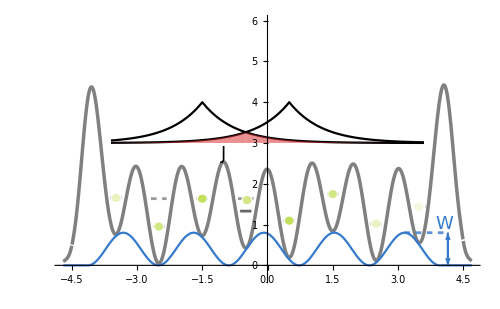
-Graphics-
-Graphics-

```mathematica
EXPPlot2=Plot[
Exp[-Abs[x-0.5]/0.75]+3,
{x,-3.6,3.6},
PlotRange-> {{-3.6,3.6},{-0.3,6}},
PlotStyle-> {RGBColor[{0,0,0}]},
Axes-> False
];
EXPPlotCB2=Plot[
{Exp[-Abs[x+1.5]/0.75]+3},
{x,-0.5,3.6},
PlotRange-> {{-3.6,-0.5},{-0.3,6}},
PlotStyle-> {Opacity[0],RGBColor[{0,0,0}]},
Axes-> False,
Filling->3,
FillingStyle-> Directive[Opacity[0.52],SpikeBallRed]
];
EXPPlotCB1=Plot[
{Exp[-Abs[x-0.5]/0.75]+3},
{x,-3.6,-0.5},
PlotRange-> {{-3.6,-0.5},{-0.3,6}},
PlotStyle-> {Opacity[0],RGBColor[{0,0,0}]},
Axes-> False,
Filling->3,
FillingStyle-> Directive[Opacity[0.52],SpikeBallRed]
];

AL2=Show[barelattV2,
LevelList,WLevels,DLevels,arcsSS,WArrows,
(*GQP1,GQP2,GQP3,GQP4,GQP5,GQP6,GQP7,GQP8,*)
QP,
(*AtomListShadow,AtomList,*)
AtomListShadowAL,AtomListAL,
labelsa,
EXPPlot,
EXPPlot2,
EXPPlotCB1,
EXPPlotCB2]
```

```mathematica
SpikeBallRed
```

Hue[0, 0.8, 0.85]

```mathematica
Integrate[x/(√(2π s^2))If[x≥0,Exp[-(x+b)^2/(2 s^2)]+Exp[-(x-b)^2/(2 s^2)],0],{x,0,100}]
```

(√(s^2) (-ⅇ^(-(-100+b)^2/(2 s^2)) √(2/π) s+2 ⅇ^(-b^2/(2 s^2)) √(2/π) s-ⅇ^(-(100+b)^2/(2 s^2)) √(2/π) s+b Erf[(100-b)/(√2 s)]+2 b Erf[b/(√2 s)]-b Erf[(100+b)/(√2 s)]))/(2 s)

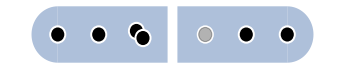
-Graphics-
-Graphics-

```mathematica
BackGrndBox=Graphics[{
Blend[{ColorData[97,"ColorList"]⟦1⟧,RGBColor["White"]},0.5],
{Rectangle[{-1.75,-0.4},{-0.075,0.4}]},
{Disk[{-1.75,0},0.4,{π/2,3π/2}]},
{Rectangle[{0.075,-0.4},{1.75,0.4}]},
{Disk[{1.75,0},0.4,{-π/2,π/2}]}
}];
N2Atoms=Graphics[{ 
RGBColor["Black"],
{Disk[{-1.75,0},{atomR,atomR}]},
{Disk[{-1.125,0},{atomR,atomR}]},
{Disk[{-0.5-0.05,0.05},{atomR,atomR}]},
{Disk[{-0.5+0.05,-0.05},{atomR,atomR}]},
{Disk[{1.125,0},{atomR,atomR}]},
{Disk[{1.75,0},{atomR,atomR}]}
}];
N2Atoms2=Graphics[{ 
RGBColor["Black"],
{Disk[{-0.5+0.05,-0.05},{atomR,atomR}]},
}];
N2AtomsShadows=Graphics[{ 
RGBColor["White"],
{Opacity[1],Disk[{-1.75,0},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-1.125,0},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-0.5-0.05,0.05},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{1.125,0},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{1.75,0},{atomShdwR,atomShdwR}]}
}];
N2AtomsShadows2=Graphics[{ 
RGBColor["White"],
{Opacity[1],Disk[{-0.5+0.05,-0.05},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{0.5,0},{atomShdwR,atomShdwR}]}
}];
rdsAndAnglsFlat={{0.1,{0.1 π,π 0.9}}};
arcsHopFlat= Graphics[{
Inset[arcsWArrows[rdsAndAnglsFlat],{0,0.3}]
}];
AtomHopped=Graphics[{
RGBColor["Black"],
Opacity[0.3],
EdgeForm[Dashing[0.005]],
Disk[{0.5,0},{atomR,atomR}]
}];

Show[BackGrndBox,N2AtomsShadows,N2Atoms,
N2AtomsShadows2,N2Atoms2,
AtomHopped,
arcsHopFlat]
(*Export["wtfpill.pdf",%,Rasterize-> False,ImageResolution-> 1000]*)
```

## Section for making protocol cartoons

0.2

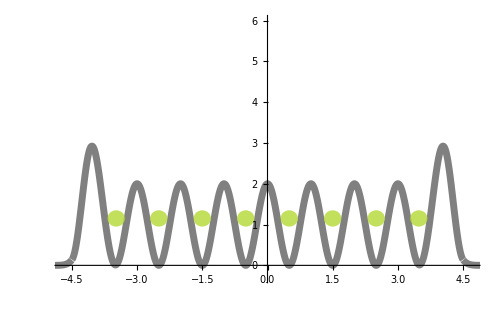

```mathematica
diskgreen= RGBColor[0.7, 0.85,0.2];
atomR=0.2
atomH=1.15;
AtomListFlat=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-3.48,atomH},{atomR,atomR}],
Disk[{-2.5,atomH},{atomR,atomR}],
Disk[{-1.5,atomH},{atomR,atomR}],
Disk[{-0.5,atomH},{atomR,atomR}],
Disk[{0.5,atomH},{atomR,atomR}],
Disk[{1.5,atomH},{atomR,atomR}],
Disk[{2.5,atomH},{atomR,atomR}],
Disk[{3.48,atomH},{atomR,atomR}]
}];


barelattVFlat=Plot[{Gauss[x,-4.1,0.2]/2+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2},
{x,-5,5},
PlotRange-> {{-5,5},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.01]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

FlatLatt=Show[
OffsetVFrame,
barelattVFlat,
AtomListFlat
]
(*Export["MBL_BHLoading.pdf",%,Rasterize-> False,ImageResolution-> 2000,ImageSize-> {63.3 ,Automatic}]*)
```

0.17

0.8

0.2

0.22

0.2266

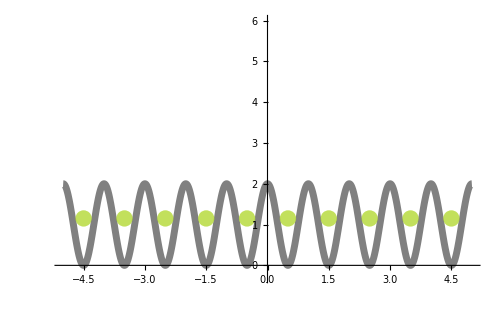

```mathematica
GR=(1+√5)/2;
Phi=0.17
WD=0.8

diskgreen= RGBColor[0.7, 0.85,0.2];
atomR=0.2
atomH=1.15;
AtomListFlat=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-4.5,atomH},{atomR,atomR}],
Disk[{-3.5,atomH},{atomR,atomR}],
Disk[{-2.5,atomH},{atomR,atomR}],
Disk[{-1.5,atomH},{atomR,atomR}],
Disk[{-0.5,atomH},{atomR,atomR}],
Disk[{0.5,atomH},{atomR,atomR}],
Disk[{1.5,atomH},{atomR,atomR}],
Disk[{2.5,atomH},{atomR,atomR}],
Disk[{3.5,atomH},{atomR,atomR}],
Disk[{4.5,atomH},{atomR,atomR}]
}];
atomShdwR=atomR 1.1


barelattVFlat2=Plot[{2*Cos[π x]^2},
{x,-5,5},
PlotRange-> {{-5,5},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.01]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

LW=atomShdwR 1.03
LevelListFlat=Graphics[{ Thickness[0.001],
RGBColor["Black"],
Opacity[0.6],
Line[{{-4.5- LW,0.95},{-4.5+ LW,0.95}}],
Line[{{-3.5- LW,0.95},{-3.5 + LW,0.95}}],
Line[{{-2.5 - LW,0.95},{-2.5+ LW,0.95}}],
Line[{{-1.5- LW,0.95},{-1.5+ LW,0.95}}],
Line[{{-0.5 - LW,0.95},{-0.5+ LW,0.95}}],
Line[{{0.5 - LW,0.95},{0.5 + LW,0.95}}],
Line[{{1.5- LW,0.95},{1.5 + LW,0.95}}],
Line[{{2.5- LW,0.95},{2.5+ LW,0.95}}],
Line[{{3.5 - LW,0.95},{3.5+ LW,0.95}}],
Line[{{4.5- LW,0.95},{4.5 + LW,0.95}}]
}];

FlatLatt=Show[
barelattVFlat2,
OffsetVFrame,
AtomListFlat
]
(*Export["MBL_BHL_MI.pdf",%,Rasterize-> False,ImageResolution-> 2000,ImageSize-> {63.3 ,Automatic}]*)
```

```mathematica
atomR
```

0.2

0.2

4.9

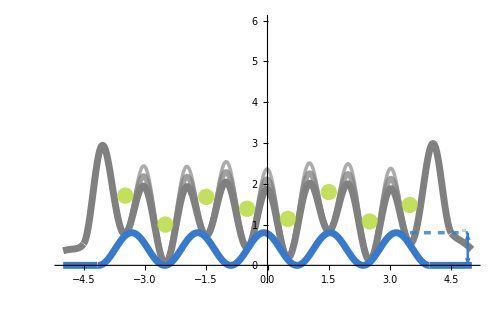

```mathematica
barelattV2q0=Plot[{Gauss[x,-4.1,0.2]/2+2*Cos[π x]^2 If[x<3.5 && x>-3.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-3.5,3.5},
PlotRange-> {{-5,5},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005],Opacity[0.65]},
AxesStyle-> Opacity[0],
ImageSize-> 500];
barelattV2q1=Plot[{Gauss[x,-4.1,0.2]/2+1.75*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-3.5,3.5},
PlotRange-> {{-5,5},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.008],Opacity[0.75]},
AxesStyle-> Opacity[0],
ImageSize-> 500];
barelattV2q2=Plot[{Gauss[x,-4.1,0.2]/2+1.5*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-5,5},
PlotRange-> {{-5,5},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.01]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

QP=Plot[{(DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-5,5},
PlotRange-> {{-5,5},{-0.3,6}},
AxesStyle-> Opacity[0],
PlotStyle-> {QPLC,Thickness[0.01]}];

atomR=0.2
atomH=1;
AtomListDis=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-3.48,atomH+DisordF[-3.5]},{atomR,atomR}],
Disk[{-2.5,atomH+DisordF[-2.5]},{atomR,atomR}],
Disk[{-1.5,atomH+DisordF[-1.5]},{atomR,atomR}],
Disk[{-0.5,atomH+DisordF[-0.5]},{atomR,atomR}],
Disk[{0.5,atomH+DisordF[0.5]},{atomR,atomR}],
Disk[{1.5,atomH+DisordF[1.5]},{atomR,atomR}],
Disk[{2.5,atomH+DisordF[2.5]},{atomR,atomR}],
Disk[{3.48,atomH+DisordF[3.5]},{atomR,atomR}]}
];
labelsbb={Graphics[{
{QPLC,Text[Style[ToExpression["W",TeXForm,HoldForm],4],{4.8,0.8},{0,-1}]}
}]};
WlenR=4.15+0.75
WArrows=Graphics[{Thickness[0.003],
QPLC,
{Arrowheads[0.022],Arrow[{{WlenR,0},{WlenR,WD}}]},
{Arrowheads[0.022],Arrow[{{WlenR,WD},{WlenR,0}}]}
}];

WLevels = Graphics[{Thickness[0.005],
QPLC,
Opacity[0.8],
Dashing[0.01],
Line[{{(2 π-Phi)/(π (GR-1)),WD},{WlenR,WD}}]
}];

MBL=Show[
barelattV2q0,
barelattV2q1,
barelattV2q2,
AtomListDis,
WLevels,
WArrows,
QP,
labelsbb]

(*Export["MBL_quench.pdf",%,Rasterize-> False,ImageResolution-> 2000,ImageSize-> {63.3 ,Automatic}]*)
```

0.16

0.8

0.14

0.16

0.18

4.9

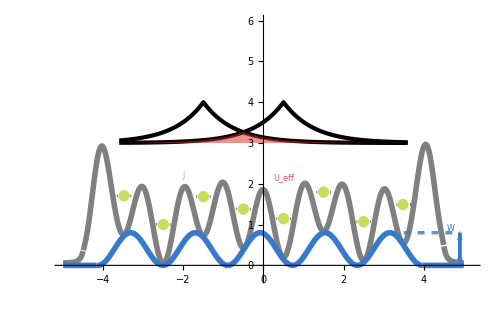
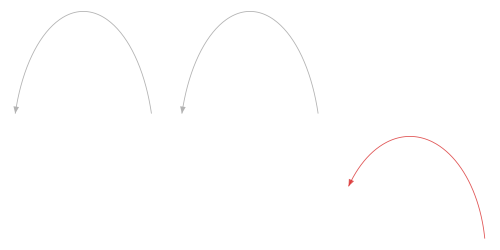

```mathematica
GR=(1+√5)/2;
Phi=0.16
WD=0.8
SmoothBox[x_,w_,dw_]:=1/π(ArcTan[(x+w)/dw]-ArcTan[(x-w)/dw])
DisordF[x_]:=WD*Cos[π x(GR-1)+Phi]^2 
DisordF1D[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x,4.5,0.05]
DisordF1DTherm[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x-1.5,2.45,0.25]

diskgreen= RGBColor[0.7, 0.85,0.2];
Jgray=0.7;
LatTH=0.008;

barelattV2=
Plot[{Gauss[x,-4.1,0.2]/2+1.5*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-5,5},
PlotRange-> {{-5,5.2},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[LatTH]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

QPLC=ColorData[94,"ColorList"]⟦1⟧;
LW=0.13;
LW2=0.17;
LW3=0.18;
WlenR=4.15;
atomR=0.10;
atomShdwR=0.13;
Uo=0.15*0.8/0.5;
Ur=0.065;
FntSz=8;

QP=Plot[{(DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-5,5},
PlotRange-> {{-5,5},{-0.3,6}},
AxesStyle-> Opacity[0],
PlotStyle-> {QPLC,Thickness[LatTH]}];

EXPPlot=Plot[
Exp[-Abs[x+1.5]/0.75]+3,
{x,-3.6,3.6},
PlotRange-> {{-3.6,3.6},{-0.3,6}},
PlotStyle-> {RGBColor[{0,0,0}],Thickness[0.006]},
AxesStyle-> Opacity[0]
];
EXPPlot2=Plot[
Exp[-Abs[x-0.5]/0.75]+3,
{x,-3.6,3.6},
PlotRange-> {{-3.6,3.6},{-0.3,6}},
PlotStyle-> {RGBColor[{0,0,0}],Thickness[0.006]},
Axes-> False
];
EXPPlotCB2=Plot[
{Exp[-Abs[x+1.5]/0.75]+3},
{x,-0.5,3.6},
PlotRange-> {{-3.6,-0.5},{-0.3,6}},
PlotStyle-> {Opacity[0],RGBColor[{0,0,0}],Thickness[0.01]},
Axes-> False,
Filling->3,
FillingStyle-> Directive[Opacity[0.52],SpikeBallRed]
];
EXPPlotCB1=Plot[
{Exp[-Abs[x-0.5]/0.75]+3},
{x,-3.6,-0.5},
PlotRange-> {{-3.6,-0.5},{-0.3,6}},
PlotStyle-> {Opacity[0],RGBColor[{0,0,0}],Thickness[0.01]},
Axes-> False,
Filling->3,
FillingStyle-> Directive[Opacity[0.52],SpikeBallRed]
];
atomR=0.14
atomShdwR=atomR+0.02
atomH=1;
AtomListAL=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-3.48,atomH+DisordF[-3.5]},{atomR,atomR}],
Disk[{-2.5,atomH+DisordF[-2.5]},{atomR,atomR}],
Disk[{-1.5,atomH+DisordF[-1.5]},{atomR,atomR}],
Disk[{-0.5,atomH+DisordF[-0.5]},{atomR,atomR}],
Disk[{0.5,atomH+DisordF[0.5]},{atomR,atomR}],
Disk[{1.5,atomH+DisordF[1.5]},{atomR,atomR}],
Disk[{2.5,atomH+DisordF[2.5]},{atomR,atomR}],
Disk[{3.48,atomH+DisordF[3.5]},{atomR,atomR}]}
];
AtomListAL2=Graphics[{ 
diskgreen,
{Opacity[0.6],Disk[{-0.5-0.03,0.95+DisordF[-0.5]+Uo-0.03},{atomR,atomR}]}
}];
AtomListShadowAL=Graphics[{ 
RGBColor["White"],
{Opacity[1],Disk[{-3.48,atomH+DisordF[-3.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-2.5,atomH+DisordF[-2.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-1.5,atomH+DisordF[-1.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-0.5,atomH+DisordF[-0.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{0.5,atomH+DisordF[0.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{1.5,atomH+DisordF[1.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{2.5,atomH+DisordF[2.5]},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{3.5,atomH+DisordF[3.5]},{atomShdwR,atomShdwR}]}
}];

AtomListShadowAL2=Graphics[{ 
RGBColor["White"],
{Opacity[1],Disk[{-0.5-0.03,0.95+DisordF[-0.5]+Uo-0.03},{atomShdwR,atomShdwR}]}
}];

USpikeBallFlat= Graphics[{SpikeBallRed,Opacity[0.52],EdgeForm[{Thickness[0.003],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-0.5,0.95+DisordF[-0.5]+Uo},0.57,0.75]}}];

LW=atomShdwR+0.02
LevelList=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,atomH+DisordF[-3.5]},{-3.48 + LW,atomH+DisordF[-3.5]}}],
Line[{{-2.5 - LW,atomH+DisordF[-2.5]},{-2.5+ LW,atomH+DisordF[-2.5]}}],
Line[{{-1.5- LW,atomH+DisordF[-1.5]},{-1.5+ LW,atomH+DisordF[-1.5]}}],
Line[{{-0.5 - LW,atomH+DisordF[-0.5]},{-0.5+ LW,atomH+DisordF[-0.5]}}],
Line[{{0.5 - LW,atomH+DisordF[0.5]},{0.5 + LW,atomH+DisordF[0.5]}}],Line[{{1.5- LW,atomH+DisordF[1.5]},{1.5 + LW,atomH+DisordF[1.5]}}],
Line[{{2.5- LW,atomH+DisordF[2.5]},{2.5+ LW,atomH+DisordF[2.5]}}],
Line[{{3.5 - LW,atomH+DisordF[3.5]},{3.5+ LW,atomH+DisordF[3.5]}}]
}];

WlenR=4.15+0.75
WArrows=Graphics[{Thickness[0.005],
QPLC,
{Arrowheads[0.02],Arrow[{{WlenR,0},{WlenR,WD}}]},
{Arrowheads[0.02],Arrow[{{WlenR,WD},{WlenR,0}}]}
}];
WLevels = Graphics[{Thickness[0.005],
QPLC,
Opacity[0.8],
Dashing[0.01],
Line[{{(2 π-Phi)/(π (GR-1)),WD},{WlenR,WD}}]
}];





ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.003],Directive[GrayLevel[Jgray],
Arrowheads[{{-0.02,0},{0.02,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.013,{0.09 π,π 0.91}}};

arcsSS=Graphics[{
{Inset[arcsWArrows[rdsAndAngls],{-2,DisordF[1.5]+1.2}],
Inset[arcsWArrows[rdsAndAngls],{-1,DisordF[1.5]+1.2}]}
}];

ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.003],Directive[Opacity[0.8],SpikeBallRed,
Arrowheads[{{-0.02,0},{0.02,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]


rdsAndAngls={{0.025,{0.05 π,π 0.8}}};
arcsUeff=Graphics[{
{
Inset[arcsWArrows[rdsAndAngls],{-0.5,DisordF[-0.5]+1.5 atomH}]
}
}];

labelsa={Graphics[{
{Opacity[0.3],Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-2,2.1},{0,-1}]},
{QPLC,Text[Style[ToExpression["W",TeXForm,HoldForm],FntSz],{WlenR-0.23,0.8},{0,-1}]},
{SpikeBallRed,Opacity[0.8],Text[Style[ToExpression["U_{eff}",TeXForm,HoldForm],FntSz],{0+0.5,DisordF[-0.5]+1.65},{0,-1}]}
}]};

AL2=Show[barelattV2,QP,
LevelList,WLevels,arcsSS,WArrows,
AtomListShadowAL,AtomListAL,
arcsUeff,
labelsa,
EXPPlot,
EXPPlot2,
EXPPlotCB1,
EXPPlotCB2]
(*Export["MBL_BH_LBIT.pdf",%,Rasterize-> False,ImageResolution-> 2000,ImageSize-> {110,Automatic}]*)
```

```mathematica
231.86/2
```

115.93

```mathematica
USpikeBall=Graphics[{SpikeBallRed,Opacity[0.62],EdgeForm[{Thickness[0.002],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-0.5,atomH+DisordF[-0.5]+Uo},0.65,0.75]}}];
```

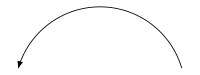
-Graphics-
-Graphics-

```mathematica
DisordF1D[x_]:= ((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x,4.5,0.05]

barelattV2=
Plot[{Gauss[x,-4.1,0.2]/2+1.5*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-5,5},
PlotRange-> {{-5,5.2},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[LatTH]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

QP=Plot[{(DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-5,5},
PlotRange-> {{-5,5},{-0.3,6}},
AxesStyle-> Opacity[0],
PlotStyle-> {QPLC,Thickness[LatTH]}];

AtomListShadow2a=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-3.48,atomH+DisordF[-3.5]},{atomShdwR,atomShdwR}],
Disk[{-2.5,atomH+DisordF[-2.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5-0.04,atomH+DisordF[-0.5]+Uo+0.03},{atomShdwR,atomShdwR}],
Disk[{0.5,atomH+DisordF[0.5]},{atomShdwR,atomShdwR}],
Disk[{1.5,atomH+DisordF[1.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,atomH+DisordF[2.5]},{atomShdwR,atomShdwR}],
Disk[{3.5,atomH+DisordF[3.5]},{atomShdwR,atomShdwR}]}];

AtomListShadow2b=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-0.5+0.04,atomH+DisordF[-0.5]+Uo-0.03},{atomShdwR,atomShdwR}],
}];

LevelList=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,atomH+DisordF[-3.5]},{-3.48 + LW,atomH+DisordF[-3.5]}}],
Line[{{-2.5 - LW,atomH+DisordF[-2.5]},{-2.5+ LW,atomH+DisordF[-2.5]}}],
Line[{{-1.5- LW,atomH+DisordF[-1.5]},{-1.5+ LW,atomH+DisordF[-1.5]}}],
Line[{{-0.5 - LW,atomH+DisordF[-0.5]},{-0.5+ LW,atomH+DisordF[-0.5]}}],
Line[{{0.5 - LW,atomH+DisordF[0.5]},{0.5 + LW,atomH+DisordF[0.5]}}],Line[{{1.5- LW,atomH+DisordF[1.5]},{1.5 + LW,atomH+DisordF[1.5]}}],
Line[{{2.5- LW,atomH+DisordF[2.5]},{2.5+ LW,atomH+DisordF[2.5]}}],
Line[{{3.5 - LW,atomH+DisordF[3.5]},{3.5+ LW,atomH+DisordF[3.5]}}]
}];

LevelList2=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.4],
Line[{{-3.48 - LW2,0.95+DisordF[-3.5]+Uo},{-3.48 + LW2,0.95+DisordF[-3.5]+Uo}}],
Line[{{-2.5 - LW2,0.95+DisordF[-2.5]+Uo},{-2.5+ LW2,0.95+DisordF[-2.5]+Uo}}],
Line[{{-1.5- LW2,0.95+DisordF[-1.5]+Uo},{-1.5+ LW2,0.95+DisordF[-1.5]+Uo}}],
Line[{{-0.5 - LW2,0.95+DisordF[-0.5]+Uo},{-0.5+ LW2,0.95+DisordF[-0.5]+Uo}}],
Line[{{0.5 - LW2,0.95+DisordF[0.5]+Uo},{0.5 + LW2,0.95+DisordF[0.5]+Uo}}],Line[{{1.5- LW2,0.95+DisordF[1.5]+Uo},{1.5 + LW2,0.95+DisordF[1.5]+Uo}}],
Line[{{2.5- LW2,0.95+DisordF[2.5]+Uo},{2.5+ LW2,0.95+DisordF[2.5]+Uo}}],
Line[{{3.5 - LW2,0.95+DisordF[3.5]+Uo},{3.5+ LW2,0.95+DisordF[3.5]+Uo}}]
}];

LevelList3=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.2],
Line[{{-3.48 - LW3,atomH+DisordF[-3.5]+3 Uo},{-3.48 + LW3,atomH+DisordF[-3.5]+3 Uo}}],
Line[{{-2.5 - LW3,atomH+DisordF[-2.5]+3 Uo},{-2.5+ LW3,atomH+DisordF[-2.5]+3 Uo}}],
Line[{{-1.5- LW3,atomH+DisordF[-1.5]+3 Uo},{-1.5+ LW3,atomH+DisordF[-1.5]+3 Uo}}],
Line[{{-0.5 - LW3,atomH+DisordF[-0.5]+3 Uo},{-0.5+ LW3,atomH+DisordF[-0.5]+3 Uo}}],
Line[{{0.5 - LW3,atomH+DisordF[0.5]+3 Uo},{0.5 + LW3,atomH+DisordF[0.5]+3 Uo}}],Line[{{1.5- LW3,atomH+DisordF[1.5]+3 Uo},{1.5 + LW3,atomH+DisordF[1.5]+3 Uo}}],
Line[{{2.5- LW3,atomH+DisordF[2.5]+3 Uo},{2.5+ LW3,atomH+DisordF[2.5]+3 Uo}}],
Line[{{3.5 - LW3,atomH+DisordF[3.5]+3 Uo},{3.5+ LW3,atomH+DisordF[3.5]+3 Uo}}]
}];

AtomList2a=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-3.48,atomH+DisordF[-3.5]},{atomR,atomR}],
Disk[{-2.5,atomH+DisordF[-2.5]},{atomR,atomR}],
Disk[{-0.5-0.04,atomH+DisordF[-0.5]+Uo+0.03},{atomR,atomR}],
Disk[{0.5,atomH+DisordF[0.5]},{atomR,atomR}],
Disk[{1.5,atomH+DisordF[1.5]},{atomR,atomR}],
Disk[{2.5,atomH+DisordF[2.5]},{atomR,atomR}],
Disk[{3.5,atomH+DisordF[3.5]},{atomR,atomR}]}];

AtomList2b=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-0.5+0.04,atomH+DisordF[-0.5]+Uo-0.03},{atomR,atomR}]}];

ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.003],Directive[GrayLevel[0],
Arrowheads[{{-0.02,0},{0.02,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.013,{0.09 π,π 0.91}}};
arcsHop = Graphics[{
Inset[arcsWArrows[rdsAndAngls],{-1,DisordF[-1.5]+1.2}]
}];

AtomList2d=Graphics[{
diskgreen,
Opacity[0.55],
EdgeForm[Directive[Dashing[0.006],Thickness[0.002]]],
Disk[{-1.5,atomH+DisordF[-1.5]},{atomR,atomR}],
Disk[{-0.5,atomH+DisordF[-0.5]},{atomR,atomR}]}];


labelsab={Graphics[{
{Opacity[1],Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-1,2.1},{0,-1}]},
{QPLC,Text[Style[ToExpression["W",TeXForm,HoldForm],FntSz],{WlenR-0.23,0.8},{0,-1}]},
{SpikeBallRed,Opacity[0.8],Text[Style[ToExpression["U",TeXForm,HoldForm],FntSz],{0,DisordF[-0.5]+1.4},{0,-1}]}
}]};

WLevels = Graphics[{Thickness[0.004],
QPLC,
Opacity[0.8],
Dashing[0.008],
Line[{{(2 π-Phi)/(π (GR-1)),WD},{WlenR,WD}}]
}];
WLevelsFlatOffset= Graphics[{Thickness[0.004],
QPLC,
Opacity[0.8],
Dashing[0.008],
Line[{{(2 π-Phi)/(π (GR-1))-3.3,DisordF[-1.5]+0.95},{WlenR,DisordF[-1.5]+0.95}}],
Line[{{(2 π-Phi)/(π (GR-1))+0.6,0.95},{WlenR,0.95}}]
}];

MBL=Show[barelattV2,
AtomList2d,
LevelList,LevelList2,LevelList3,
WLevels,
arcsHop,WArrows,
QP,
USpikeBall,
AtomListShadow2b,AtomList2b,
AtomListShadow2a,AtomList2a,
labelsab]

(*Export["MBL_BH_PROTOCOL.pdf",%,Rasterize-> False,ImageResolution-> 2000,ImageSize-> {110,Automatic}]*)
```

## Make ETH Cartoons

```mathematica
GR=(1+√5)/2;
Phi=0.16
WD=0.1

diskgreen= RGBColor[0.7, 0.85,0.2];

QPLC=ColorData[94,"ColorList"]⟦1⟧;
LW=0.13;
LW2=0.17;
LW3=0.18;
WlenR=4.15;
atomR=0.10;
atomShdwR=0.13;
Uo=0
Ur=0.065;
FntSz=18;
```

0.16

0.1

0

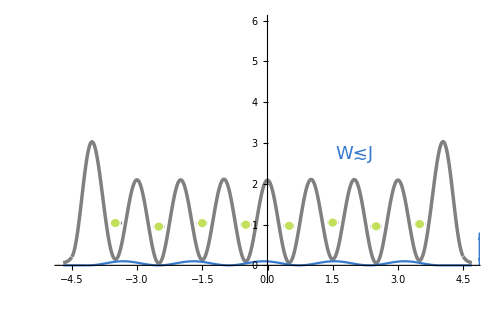

ETH_Latt_Combo_noU0.pdf

```mathematica
SpikeBallRed=ColorData[93,"ColorList"]⟦1⟧;
USpikeBall=Graphics[{SpikeBallRed,Opacity[0.52],EdgeForm[{Thickness[0.000001],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-0.5,0.95+DisordF[-0.5]+Uo},0.52,0.75]}}];

DisordF[x_]:=WD*Cos[π x(GR-1)+Phi]^2 

DisordF1D[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x,4.5,0.05]

barelattV2=Plot[{Gauss[x,-4.1,0.2]/2+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

QP=Plot[{( DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-4.7,4.7},
AxesStyle-> Opacity[0],
PlotStyle-> {{QPLC}}];

LevelList=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,0.95+DisordF[-3.5]},{-3.48 + LW,0.95+DisordF[-3.5]}}],
Line[{{-2.5 - LW,0.95+DisordF[-2.5]},{-2.5+ LW,0.95+DisordF[-2.5]}}],
Line[{{-1.5- LW,0.95+DisordF[-1.5]},{-1.5+ LW,0.95+DisordF[-1.5]}}],
Line[{{-0.5 - LW,0.95+DisordF[-0.5]},{-0.5+ LW,0.95+DisordF[-0.5]}}],
Line[{{0.5 - LW,0.95+DisordF[0.5]},{0.5 + LW,0.95+DisordF[0.5]}}],Line[{{1.5- LW,0.95+DisordF[1.5]},{1.5 + LW,0.95+DisordF[1.5]}}],
Line[{{2.5- LW,0.95+DisordF[2.5]},{2.5+ LW,0.95+DisordF[2.5]}}],
Line[{{3.5 - LW,0.95+DisordF[3.5]},{3.5+ LW,0.95+DisordF[3.5]}}]
}];




AtomListShadow2a=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-3.5,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomShdwR,atomShdwR}]}];
AtomListShadow2b=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-2.5+0.04,0.95+DisordF[-2.5]+Uo-0.03},{atomShdwR,atomShdwR}],
}];


AtomList2a=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-3.5,0.95+DisordF[-3.5]},{atomR,atomR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomR,atomR}]}];


labelsb={Graphics[{
{QPLC,Text[Style[ToExpression["W \\lesssim J",TeXForm,HoldForm],FntSz],{2,2.5},{0,-1}]}
}]};

ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[GrayLevel[0],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.075,{0.2π,π 0.8}}};
arcsHop = Graphics[{
Inset[arcsWArrows[rdsAndAngls],{-3,DisordF[-1.5]+1.3}]
}];


MBL=Show[barelattV2,
LevelList,
WArrows,
QP,
AtomListShadow2a,AtomList2a,
labelsb]

Export["ETH_Latt_Combo_noU0.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

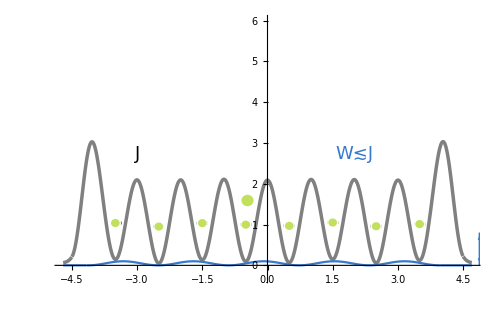
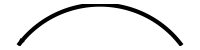

ETH_Latt_Combo_noU1.pdf

```mathematica
SpikeBallRed=ColorData[93,"ColorList"]⟦1⟧;
USpikeBall=Graphics[{SpikeBallRed,Opacity[0.52],EdgeForm[{Thickness[0.000001],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-0.5,0.95+DisordF[-0.5]+Uo},0.52,0.75]}}];

DisordF[x_]:=WD*Cos[π x(GR-1)+Phi]^2 

DisordF1D[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x,4.5,0.05]

barelattV2=Plot[{Gauss[x,-4.1,0.2]/2+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

QP=Plot[{( DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-4.7,4.7},
AxesStyle-> Opacity[0],
PlotStyle-> {{QPLC}}];

LevelList=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,0.95+DisordF[-3.5]},{-3.48 + LW,0.95+DisordF[-3.5]}}],
Line[{{-2.5 - LW,0.95+DisordF[-2.5]},{-2.5+ LW,0.95+DisordF[-2.5]}}],
Line[{{-1.5- LW,0.95+DisordF[-1.5]},{-1.5+ LW,0.95+DisordF[-1.5]}}],
Line[{{-0.5 - LW,0.95+DisordF[-0.5]},{-0.5+ LW,0.95+DisordF[-0.5]}}],
Line[{{0.5 - LW,0.95+DisordF[0.5]},{0.5 + LW,0.95+DisordF[0.5]}}],Line[{{1.5- LW,0.95+DisordF[1.5]},{1.5 + LW,0.95+DisordF[1.5]}}],
Line[{{2.5- LW,0.95+DisordF[2.5]},{2.5+ LW,0.95+DisordF[2.5]}}],
Line[{{3.5 - LW,0.95+DisordF[3.5]},{3.5+ LW,0.95+DisordF[3.5]}}]
}];




AtomListShadow2a=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-3.5,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomShdwR,atomShdwR}]}];
AtomListShadow2b=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-2.5+0.04,0.95+DisordF[-2.5]+Uo-0.03},{atomShdwR,atomShdwR}],
}];


AtomList2a=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-3.5,0.95+DisordF[-3.5]},{atomR,atomR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomR,atomR}]}];


labelsb={Graphics[{
{Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-3,2.5},{0,-1}]},
{QPLC,Text[Style[ToExpression["W \\lesssim J",TeXForm,HoldForm],FntSz],{2,2.5},{0,-1}]}
}]};

ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[GrayLevel[0],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.075,{0.2π,π 0.8}}};
arcsHop = Graphics[{
Inset[arcsWArrows[rdsAndAngls],{-3,DisordF[-1.5]+1.3}]
}];


MBL=Show[barelattV2,
LevelList,
arcsHop,WArrows,
QP,
AtomListShadow2b,AtomList2b,
AtomListShadow2a,AtomList2a,
labelsb]

Export["ETH_Latt_Combo_noU1.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

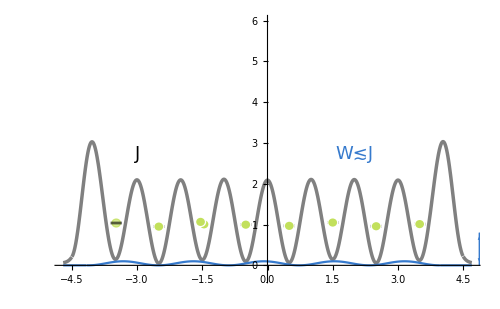
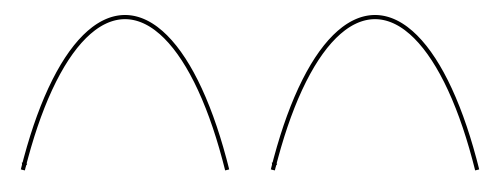

ETH_Latt_Combo_noU2.pdf

```mathematica
SpikeBallRed=ColorData[93,"ColorList"]⟦1⟧;
USpikeBall=Graphics[{SpikeBallRed,Opacity[0.52],EdgeForm[{Thickness[0.000001],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-0.5,0.95+DisordF[-0.5]+Uo},0.52,0.75]}}];

DisordF[x_]:=WD*Cos[π x(GR-1)+Phi]^2 

DisordF1D[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x,4.5,0.05]

barelattV2=Plot[{Gauss[x,-4.1,0.2]/2+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

QP=Plot[{( DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-4.7,4.7},
AxesStyle-> Opacity[0],
PlotStyle-> {{QPLC}}];

LevelList=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,0.95+DisordF[-3.5]},{-3.48 + LW,0.95+DisordF[-3.5]}}],
Line[{{-2.5 - LW,0.95+DisordF[-2.5]},{-2.5+ LW,0.95+DisordF[-2.5]}}],
Line[{{-1.5- LW,0.95+DisordF[-1.5]},{-1.5+ LW,0.95+DisordF[-1.5]}}],
Line[{{-0.5 - LW,0.95+DisordF[-0.5]},{-0.5+ LW,0.95+DisordF[-0.5]}}],
Line[{{0.5 - LW,0.95+DisordF[0.5]},{0.5 + LW,0.95+DisordF[0.5]}}],Line[{{1.5- LW,0.95+DisordF[1.5]},{1.5 + LW,0.95+DisordF[1.5]}}],
Line[{{2.5- LW,0.95+DisordF[2.5]},{2.5+ LW,0.95+DisordF[2.5]}}],
Line[{{3.5 - LW,0.95+DisordF[3.5]},{3.5+ LW,0.95+DisordF[3.5]}}]
}];


AtomList2d=Graphics[{
diskgreen,
Opacity[0.55],
EdgeForm[Dashing[0.005]],
Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}]}];

AtomListShadow2d=Graphics[{ 
RGBColor["White"],
Opacity[0.4],
Disk[{-3.48,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}]
}];

AtomListShadow2a=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-1.5-0.04,0.95+DisordF[-1.5]+Uo+0.03},{atomShdwR,atomShdwR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomShdwR,atomShdwR}]}];

AtomListShadow2b=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-1.5+0.04,0.95+DisordF[-1.5]+Uo-0.03},{atomShdwR,atomShdwR}],
}];


AtomList2a=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-1.5-0.04,0.95+DisordF[-1.5]+Uo+0.03},{atomR,atomR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomR,atomR}]}];

AtomList2b=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-1.5+0.04,0.95+DisordF[-1.5]+Uo-0.03},{atomR,atomR}]
}];

labelsb={Graphics[{
{Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-3,2.5},{0,-1}]},
{QPLC,Text[Style[ToExpression["W \\lesssim J",TeXForm,HoldForm],FntSz],{2,2.5},{0,-1}]}
}]};

ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[GrayLevel[0],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.075,{0.2π,π 0.8}}};
arcsHop = Graphics[{
Inset[arcsWArrows[rdsAndAngls],{-3,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{-2,DisordF[-1.5]+1.3}]
}];


(*LevelList2,LevelList3*)
MBL=Show[barelattV2,
AtomListShadow2d,AtomList2d,
LevelList,
arcsHop,WArrows,
QP,
AtomListShadow2b,AtomList2b,
AtomListShadow2a,AtomList2a,
labelsb]

Export["ETH_Latt_Combo_noU2.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

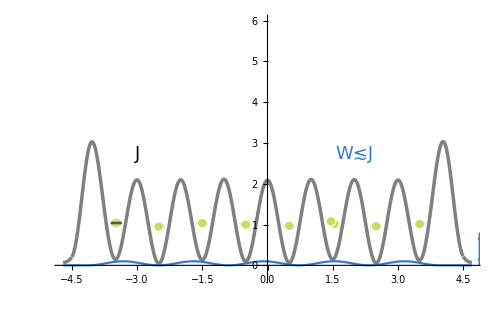
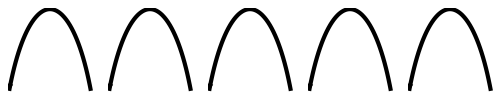

ETH_Latt_Combo_noU3.pdf

```mathematica
SpikeBallRed=ColorData[93,"ColorList"]⟦1⟧;
USpikeBall=Graphics[{SpikeBallRed,Opacity[0.52],EdgeForm[{Thickness[0.000001],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-0.5,0.95+DisordF[-0.5]+Uo},0.52,0.75]}}];

DisordF[x_]:=WD*Cos[π x(GR-1)+Phi]^2 

DisordF1D[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x,4.5,0.05]

barelattV2=Plot[{Gauss[x,-4.1,0.2]/2+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

QP=Plot[{( DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-4.7,4.7},
AxesStyle-> Opacity[0],
PlotStyle-> {{QPLC}}];

LevelList=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,0.95+DisordF[-3.5]},{-3.48 + LW,0.95+DisordF[-3.5]}}],
Line[{{-2.5 - LW,0.95+DisordF[-2.5]},{-2.5+ LW,0.95+DisordF[-2.5]}}],
Line[{{-1.5- LW,0.95+DisordF[-1.5]},{-1.5+ LW,0.95+DisordF[-1.5]}}],
Line[{{-0.5 - LW,0.95+DisordF[-0.5]},{-0.5+ LW,0.95+DisordF[-0.5]}}],
Line[{{0.5 - LW,0.95+DisordF[0.5]},{0.5 + LW,0.95+DisordF[0.5]}}],Line[{{1.5- LW,0.95+DisordF[1.5]},{1.5 + LW,0.95+DisordF[1.5]}}],
Line[{{2.5- LW,0.95+DisordF[2.5]},{2.5+ LW,0.95+DisordF[2.5]}}],
Line[{{3.5 - LW,0.95+DisordF[3.5]},{3.5+ LW,0.95+DisordF[3.5]}}]
}];


AtomList2d=Graphics[{
diskgreen,
Opacity[0.55],
EdgeForm[Dashing[0.005]],
Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}]}];

AtomListShadow2d=Graphics[{ 
RGBColor["White"],
Opacity[0.4],
Disk[{-3.48,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}]
}];

AtomListShadow2a=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{1.5-0.04,0.95+DisordF[1.5]+Uo+0.03},{atomShdwR,atomShdwR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomShdwR,atomShdwR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomShdwR,atomShdwR}]}];
AtomListShadow2b=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{1.5+0.04,0.95+DisordF[1.5]+Uo-0.03},{atomShdwR,atomShdwR}],
}];


AtomList2a=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{1.5-0.04,0.95+DisordF[1.5]+Uo+0.03},{atomR,atomR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomR,atomR}]}];

AtomList2b=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{1.5+0.04,0.95+DisordF[1.5]+Uo-0.03},{atomR,atomR}]
}];

labelsb={Graphics[{
{Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-3,2.5},{0,-1}]},
{QPLC,Text[Style[ToExpression["W \\lesssim J",TeXForm,HoldForm],FntSz],{2,2.5},{0,-1}]}
}]};

ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[GrayLevel[0],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.075,{0.2π,π 0.8}}};
arcsHop = Graphics[{
Inset[arcsWArrows[rdsAndAngls],{-3,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{-2,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{-1,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{0,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{1,DisordF[-1.5]+1.3}]
}];

MBL=Show[barelattV2,
AtomListShadow2d,AtomList2d,
LevelList,
arcsHop,WArrows,
QP,
AtomListShadow2b,AtomList2b,
AtomListShadow2a,AtomList2a,
labelsb]

Export["ETH_Latt_Combo_noU3.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

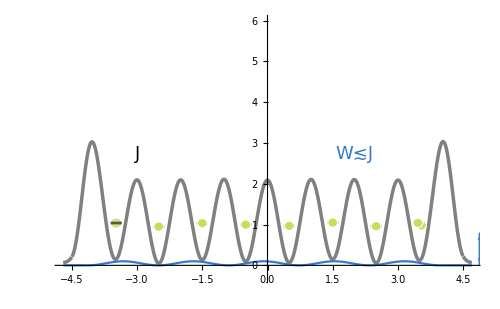
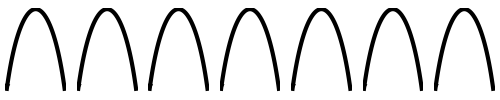

ETH_Latt_Combo_noU4.pdf

```mathematica
SpikeBallRed=ColorData[93,"ColorList"]⟦1⟧;
USpikeBall=Graphics[{SpikeBallRed,Opacity[0.52],EdgeForm[{Thickness[0.000001],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-0.5,0.95+DisordF[-0.5]+Uo},0.52,0.75]}}];

DisordF[x_]:=WD*Cos[π x(GR-1)+Phi]^2 

DisordF1D[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x,4.5,0.05]

barelattV2=Plot[{Gauss[x,-4.1,0.2]/2+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

QP=Plot[{( DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-4.7,4.7},
AxesStyle-> Opacity[0],
PlotStyle-> {{QPLC}}];

LevelList=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,0.95+DisordF[-3.5]},{-3.48 + LW,0.95+DisordF[-3.5]}}],
Line[{{-2.5 - LW,0.95+DisordF[-2.5]},{-2.5+ LW,0.95+DisordF[-2.5]}}],
Line[{{-1.5- LW,0.95+DisordF[-1.5]},{-1.5+ LW,0.95+DisordF[-1.5]}}],
Line[{{-0.5 - LW,0.95+DisordF[-0.5]},{-0.5+ LW,0.95+DisordF[-0.5]}}],
Line[{{0.5 - LW,0.95+DisordF[0.5]},{0.5 + LW,0.95+DisordF[0.5]}}],Line[{{1.5- LW,0.95+DisordF[1.5]},{1.5 + LW,0.95+DisordF[1.5]}}],
Line[{{2.5- LW,0.95+DisordF[2.5]},{2.5+ LW,0.95+DisordF[2.5]}}],
Line[{{3.5 - LW,0.95+DisordF[3.5]},{3.5+ LW,0.95+DisordF[3.5]}}]
}];


AtomList2d=Graphics[{
diskgreen,
Opacity[0.55],
EdgeForm[Dashing[0.005]],
Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}]}];

AtomListShadow2d=Graphics[{ 
RGBColor["White"],
Opacity[0.4],
Disk[{-3.48,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}]
}];

AtomListShadow2a=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{3.5-0.04,0.95+DisordF[3.5]+Uo+0.03},{atomShdwR,atomShdwR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomShdwR,atomShdwR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}]}];
AtomListShadow2b=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{3.5+0.04,0.95+DisordF[3.5]+Uo-0.03},{atomShdwR,atomShdwR}],
}];


AtomList2a=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{3.5-0.04,0.95+DisordF[3.5]+Uo+0.03},{atomR,atomR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}]}];

AtomList2b=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{3.5+0.04,0.95+DisordF[3.5]+Uo-0.03},{atomR,atomR}]
}];

labelsb={Graphics[{
{Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-3,2.5},{0,-1}]},
{QPLC,Text[Style[ToExpression["W \\lesssim J",TeXForm,HoldForm],FntSz],{2,2.5},{0,-1}]}
}]};

ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[GrayLevel[0],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.075,{0.2π,π 0.8}}};
arcsHop = Graphics[{
Inset[arcsWArrows[rdsAndAngls],{-3,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{-2,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{-1,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{0,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{1,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{2,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{3,DisordF[-1.5]+1.3}]
}];

MBL=Show[barelattV2,
AtomListShadow2d,AtomList2d,
LevelList,
arcsHop,WArrows,
QP,
AtomListShadow2b,AtomList2b,
AtomListShadow2a,AtomList2a,
labelsb]

Export["ETH_Latt_Combo_noU4.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

```mathematica
"ETH_Latt_Combo_noU4.pdf"
```

ETH_Latt_Combo_noU4.pdf

## Make ETH Cartoons + U

```mathematica
GR=(1+√5)/2;
Phi=0.16
WD=0.1

diskgreen= RGBColor[0.7, 0.85,0.2];

QPLC=ColorData[94,"ColorList"]⟦1⟧;
LW=0.13;
LW2=0.17;
LW3=0.18;
WlenR=4.15;
atomR=0.10;
atomShdwR=0.13;
Uo=0.3
Ur=0.065;
FntSz=18;
```

0.16

0.1

0.3

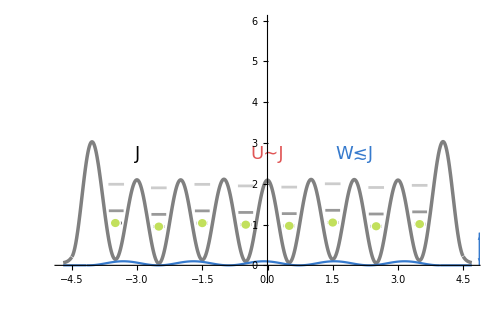
-Graphics-
-Graphics-

ETH_Latt_Combo_U1.pdf

```mathematica
SpikeBallRed=ColorData[93,"ColorList"]⟦1⟧;
USpikeBall=Graphics[{SpikeBallRed,Opacity[0.52],EdgeForm[{Thickness[0.000001],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-0.5,0.95+DisordF[-0.5]+Uo},0.52,0.75]}}];

DisordF[x_]:=WD*Cos[π x(GR-1)+Phi]^2 

DisordF1D[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x,4.5,0.05]

barelattV2=Plot[{Gauss[x,-4.1,0.2]/2+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

QP=Plot[{( DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-4.7,4.7},
AxesStyle-> Opacity[0],
PlotStyle-> {{QPLC}}];

LevelList=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,0.95+DisordF[-3.5]},{-3.48 + LW,0.95+DisordF[-3.5]}}],
Line[{{-2.5 - LW,0.95+DisordF[-2.5]},{-2.5+ LW,0.95+DisordF[-2.5]}}],
Line[{{-1.5- LW,0.95+DisordF[-1.5]},{-1.5+ LW,0.95+DisordF[-1.5]}}],
Line[{{-0.5 - LW,0.95+DisordF[-0.5]},{-0.5+ LW,0.95+DisordF[-0.5]}}],
Line[{{0.5 - LW,0.95+DisordF[0.5]},{0.5 + LW,0.95+DisordF[0.5]}}],Line[{{1.5- LW,0.95+DisordF[1.5]},{1.5 + LW,0.95+DisordF[1.5]}}],
Line[{{2.5- LW,0.95+DisordF[2.5]},{2.5+ LW,0.95+DisordF[2.5]}}],
Line[{{3.5 - LW,0.95+DisordF[3.5]},{3.5+ LW,0.95+DisordF[3.5]}}]
}];

LevelList2=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.4],
Line[{{-3.48 - LW2,0.95+DisordF[-3.5]+Uo},{-3.48 + LW2,0.95+DisordF[-3.5]+Uo}}],
Line[{{-2.5 - LW2,0.95+DisordF[-2.5]+Uo},{-2.5+ LW2,0.95+DisordF[-2.5]+Uo}}],
Line[{{-1.5- LW2,0.95+DisordF[-1.5]+Uo},{-1.5+ LW2,0.95+DisordF[-1.5]+Uo}}],
Line[{{-0.5 - LW2,0.95+DisordF[-0.5]+Uo},{-0.5+ LW2,0.95+DisordF[-0.5]+Uo}}],
Line[{{0.5 - LW2,0.95+DisordF[0.5]+Uo},{0.5 + LW2,0.95+DisordF[0.5]+Uo}}],Line[{{1.5- LW2,0.95+DisordF[1.5]+Uo},{1.5 + LW2,0.95+DisordF[1.5]+Uo}}],
Line[{{2.5- LW2,0.95+DisordF[2.5]+Uo},{2.5+ LW2,0.95+DisordF[2.5]+Uo}}],
Line[{{3.5 - LW2,0.95+DisordF[3.5]+Uo},{3.5+ LW2,0.95+DisordF[3.5]+Uo}}]
}];

LevelList3=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.2],
Line[{{-3.48 - LW3,atomH+DisordF[-3.5]+3 Uo},{-3.48 + LW3,atomH+DisordF[-3.5]+3 Uo}}],
Line[{{-2.5 - LW3,atomH+DisordF[-2.5]+3 Uo},{-2.5+ LW3,atomH+DisordF[-2.5]+3 Uo}}],
Line[{{-1.5- LW3,atomH+DisordF[-1.5]+3 Uo},{-1.5+ LW3,atomH+DisordF[-1.5]+3 Uo}}],
Line[{{-0.5 - LW3,atomH+DisordF[-0.5]+3 Uo},{-0.5+ LW3,atomH+DisordF[-0.5]+3 Uo}}],
Line[{{0.5 - LW3,atomH+DisordF[0.5]+3 Uo},{0.5 + LW3,atomH+DisordF[0.5]+3 Uo}}],Line[{{1.5- LW3,atomH+DisordF[1.5]+3 Uo},{1.5 + LW3,atomH+DisordF[1.5]+3 Uo}}],
Line[{{2.5- LW3,atomH+DisordF[2.5]+3 Uo},{2.5+ LW3,atomH+DisordF[2.5]+3 Uo}}],
Line[{{3.5 - LW3,atomH+DisordF[3.5]+3 Uo},{3.5+ LW3,atomH+DisordF[3.5]+3 Uo}}]
}];



AtomListShadow2a=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-3.5,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomShdwR,atomShdwR}]}];



AtomList2a=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-3.5,0.95+DisordF[-3.5]},{atomR,atomR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomR,atomR}]}];


labelsb={Graphics[{
{Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-3,2.5},{0,-1}]},
{QPLC,Text[Style[ToExpression["W \\lesssim J",TeXForm,HoldForm],FntSz],{2,2.5},{0,-1}]},
{SpikeBallRed,Opacity[0.8],Text[Style[ToExpression["U \\sim J",TeXForm,HoldForm],FntSz],{0,2.5},{0,-1}]}
}]};

ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[GrayLevel[0],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.075,{0.2π,π 0.8}}};
arcsHop = Graphics[{
Inset[arcsWArrows[rdsAndAngls],{-3,DisordF[-1.5]+1.3}]
}];


MBL=Show[barelattV2,
LevelList,LevelList2,LevelList3,
arcsHop,WArrows,
QP,
AtomListShadow2a,AtomList2a,
labelsb]

Export["ETH_Latt_Combo_U1.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

```mathematica
DisordF[x_]:=WD*Cos[π x(GR-1)+Phi]^2 

DisordF1D[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x,4.5,0.05]

barelattV2=Plot[{Gauss[x,-4.1,0.2]/2+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

QP=Plot[{( DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-4.7,4.7},
AxesStyle-> Opacity[0],
PlotStyle-> {{QPLC}}];

LevelList=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,0.95+DisordF[-3.5]},{-3.48 + LW,0.95+DisordF[-3.5]}}],
Line[{{-2.5 - LW,0.95+DisordF[-2.5]},{-2.5+ LW,0.95+DisordF[-2.5]}}],
Line[{{-1.5- LW,0.95+DisordF[-1.5]},{-1.5+ LW,0.95+DisordF[-1.5]}}],
Line[{{-0.5 - LW,0.95+DisordF[-0.5]},{-0.5+ LW,0.95+DisordF[-0.5]}}],
Line[{{0.5 - LW,0.95+DisordF[0.5]},{0.5 + LW,0.95+DisordF[0.5]}}],Line[{{1.5- LW,0.95+DisordF[1.5]},{1.5 + LW,0.95+DisordF[1.5]}}],
Line[{{2.5- LW,0.95+DisordF[2.5]},{2.5+ LW,0.95+DisordF[2.5]}}],
Line[{{3.5 - LW,0.95+DisordF[3.5]},{3.5+ LW,0.95+DisordF[3.5]}}]
}];


AtomList2d=Graphics[{
diskgreen,
Opacity[0.55],
EdgeForm[Dashing[0.005]],
Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}]}];

AtomListShadow2d=Graphics[{ 
RGBColor["White"],
Opacity[0.4],
Disk[{-3.48,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}]
}];

AtomListShadow2a=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-1.5-0.04,0.95+DisordF[-1.5]+Uo+0.03},{atomShdwR,atomShdwR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomShdwR,atomShdwR}]}];

AtomListShadow2b=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-1.5+0.04,0.95+DisordF[-1.5]+Uo-0.03},{atomShdwR,atomShdwR}],
}];


AtomList2a=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-1.5-0.04,0.95+DisordF[-1.5]+Uo+0.03},{atomR,atomR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomR,atomR}]}];

AtomList2b=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-1.5+0.04,0.95+DisordF[-1.5]+Uo-0.03},{atomR,atomR}]
}];

labelsb={Graphics[{
{Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-3,2.5},{0,-1}]},
{QPLC,Text[Style[ToExpression["W \\lesssim J",TeXForm,HoldForm],FntSz],{2,2.5},{0,-1}]},
{SpikeBallRed,Opacity[0.8],Text[Style[ToExpression["U \\sim J",TeXForm,HoldForm],FntSz],{0,2.5},{0,-1}]}
}]};

ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[GrayLevel[0],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.075,{0.2π,π 0.8}}};
arcsHop = Graphics[{
Inset[arcsWArrows[rdsAndAngls],{-3,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{-2,DisordF[-1.5]+1.3}]
}];


USpikeBall=Graphics[{SpikeBallRed,Opacity[0.62],EdgeForm[{Thickness[0.002],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-1.5,atomH+DisordF[-1.5]+Uo},0.65,0.75]}}];

MBL=Show[barelattV2,
AtomListShadow2d,AtomList2d,
LevelList,LevelList2,LevelList3,
arcsHop,WArrows,
QP,USpikeBall,
AtomListShadow2b,AtomList2b,
AtomListShadow2a,AtomList2a,
labelsb]

Export["ETH_Latt_Combo_U2.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

-Graphics-
-Graphics-

ETH_Latt_Combo_U2.pdf

```mathematica
DisordF[x_]:=WD*Cos[π x(GR-1)+Phi]^2 

DisordF1D[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x,4.5,0.05]

barelattV2=Plot[{Gauss[x,-4.1,0.2]/2+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

QP=Plot[{( DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-4.7,4.7},
AxesStyle-> Opacity[0],
PlotStyle-> {{QPLC}}];

LevelList=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,0.95+DisordF[-3.5]},{-3.48 + LW,0.95+DisordF[-3.5]}}],
Line[{{-2.5 - LW,0.95+DisordF[-2.5]},{-2.5+ LW,0.95+DisordF[-2.5]}}],
Line[{{-1.5- LW,0.95+DisordF[-1.5]},{-1.5+ LW,0.95+DisordF[-1.5]}}],
Line[{{-0.5 - LW,0.95+DisordF[-0.5]},{-0.5+ LW,0.95+DisordF[-0.5]}}],
Line[{{0.5 - LW,0.95+DisordF[0.5]},{0.5 + LW,0.95+DisordF[0.5]}}],Line[{{1.5- LW,0.95+DisordF[1.5]},{1.5 + LW,0.95+DisordF[1.5]}}],
Line[{{2.5- LW,0.95+DisordF[2.5]},{2.5+ LW,0.95+DisordF[2.5]}}],
Line[{{3.5 - LW,0.95+DisordF[3.5]},{3.5+ LW,0.95+DisordF[3.5]}}]
}];


AtomList2d=Graphics[{
diskgreen,
Opacity[0.55],
EdgeForm[Dashing[0.005]],
Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}]}];

AtomListShadow2d=Graphics[{ 
RGBColor["White"],
Opacity[0.4],
Disk[{-3.48,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}]
}];

AtomListShadow2a=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{1.5-0.04,0.95+DisordF[1.5]+Uo+0.03},{atomShdwR,atomShdwR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomShdwR,atomShdwR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomShdwR,atomShdwR}]}];
AtomListShadow2b=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{1.5+0.04,0.95+DisordF[1.5]+Uo-0.03},{atomShdwR,atomShdwR}],
}];


AtomList2a=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{1.5-0.04,0.95+DisordF[1.5]+Uo+0.03},{atomR,atomR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomR,atomR}]}];

AtomList2b=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{1.5+0.04,0.95+DisordF[1.5]+Uo-0.03},{atomR,atomR}]
}];

labelsb={Graphics[{
{Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-3,2.5},{0,-1}]},
{QPLC,Text[Style[ToExpression["W \\lesssim J",TeXForm,HoldForm],FntSz],{2,2.5},{0,-1}]},
{SpikeBallRed,Opacity[0.8],Text[Style[ToExpression["U \\sim J",TeXForm,HoldForm],FntSz],{0,2.5},{0,-1}]}
}]};

ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[GrayLevel[0],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.075,{0.2π,π 0.8}}};
arcsHop = Graphics[{
Inset[arcsWArrows[rdsAndAngls],{-3,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{-2,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{-1,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{0,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{1,DisordF[-1.5]+1.3}]
}];



USpikeBall=Graphics[{SpikeBallRed,Opacity[0.62],EdgeForm[{Thickness[0.002],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{1.5,atomH+DisordF[1.5]+Uo},0.65,0.75]}}];

MBL=Show[barelattV2,
AtomListShadow2d,AtomList2d,
LevelList,LevelList2,LevelList3,
arcsHop,WArrows,
QP,USpikeBall,
AtomListShadow2b,AtomList2b,
AtomListShadow2a,AtomList2a,
labelsb]

Export["ETH_Latt_Combo_U3.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

-Graphics-
-Graphics-

ETH_Latt_Combo_U3.pdf

```mathematica
DisordF[x_]:=WD*Cos[π x(GR-1)+Phi]^2 

DisordF1D[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x,4.5,0.05]

barelattV2=Plot[{Gauss[x,-4.1,0.2]/2+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

QP=Plot[{( DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-4.7,4.7},
AxesStyle-> Opacity[0],
PlotStyle-> {{QPLC}}];

LevelList=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,0.95+DisordF[-3.5]},{-3.48 + LW,0.95+DisordF[-3.5]}}],
Line[{{-2.5 - LW,0.95+DisordF[-2.5]},{-2.5+ LW,0.95+DisordF[-2.5]}}],
Line[{{-1.5- LW,0.95+DisordF[-1.5]},{-1.5+ LW,0.95+DisordF[-1.5]}}],
Line[{{-0.5 - LW,0.95+DisordF[-0.5]},{-0.5+ LW,0.95+DisordF[-0.5]}}],
Line[{{0.5 - LW,0.95+DisordF[0.5]},{0.5 + LW,0.95+DisordF[0.5]}}],Line[{{1.5- LW,0.95+DisordF[1.5]},{1.5 + LW,0.95+DisordF[1.5]}}],
Line[{{2.5- LW,0.95+DisordF[2.5]},{2.5+ LW,0.95+DisordF[2.5]}}],
Line[{{3.5 - LW,0.95+DisordF[3.5]},{3.5+ LW,0.95+DisordF[3.5]}}]
}];


AtomList2d=Graphics[{
diskgreen,
Opacity[0.55],
EdgeForm[Dashing[0.005]],
Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}]}];

AtomListShadow2d=Graphics[{ 
RGBColor["White"],
Opacity[0.4],
Disk[{-3.48,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}]
}];

AtomListShadow2a=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{3.5-0.04,0.95+DisordF[3.5]+Uo+0.03},{atomShdwR,atomShdwR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomShdwR,atomShdwR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}]}];
AtomListShadow2b=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{3.5+0.04,0.95+DisordF[3.5]+Uo-0.03},{atomShdwR,atomShdwR}],
}];


AtomList2a=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{3.5-0.04,0.95+DisordF[3.5]+Uo+0.03},{atomR,atomR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}]}];

AtomList2b=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{3.5+0.04,0.95+DisordF[3.5]+Uo-0.03},{atomR,atomR}]
}];

labelsb={Graphics[{
{Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-3,2.5},{0,-1}]},
{QPLC,Text[Style[ToExpression["W \\lesssim J",TeXForm,HoldForm],FntSz],{2,2.5},{0,-1}]},
{SpikeBallRed,Opacity[0.8],Text[Style[ToExpression["U \\sim J",TeXForm,HoldForm],FntSz],{0,2.5},{0,-1}]}
}]};


ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[GrayLevel[0],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.075,{0.2π,π 0.8}}};
arcsHop = Graphics[{
Inset[arcsWArrows[rdsAndAngls],{-3,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{-2,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{-1,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{0,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{1,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{2,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{3,DisordF[-1.5]+1.3}]
}];




USpikeBall=Graphics[{SpikeBallRed,Opacity[0.62],EdgeForm[{Thickness[0.002],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{3.5,atomH+DisordF[3.5]+Uo},0.65,0.75]}}];


MBL=Show[barelattV2,
AtomListShadow2d,AtomList2d,
LevelList,LevelList2,LevelList3,
arcsHop,WArrows,
QP,USpikeBall,
AtomListShadow2b,AtomList2b,
AtomListShadow2a,AtomList2a,
labelsb]

Export["ETH_Latt_Combo_U4.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

-Graphics-
-Graphics-

ETH_Latt_Combo_U4.pdf

## Make MBL Cartoons

```mathematica
GR=(1+√5)/2;
Phi=0.25
WD=0.8

diskgreen= RGBColor[0.7, 0.85,0.2];

QPLC=ColorData[94,"ColorList"]⟦1⟧;
LW=0.13;
LW2=0.17;
LW3=0.18;
WlenR=4.15;
atomR=0.10;
atomShdwR=0.13;
Uo=0
Ur=0.065;
FntSz=18;
```

0.25

0.8

0

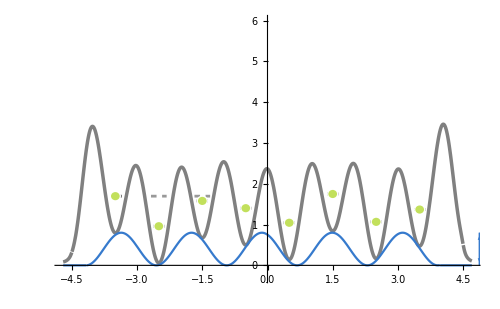

MBL_Latt_Combo_noU0.pdf

```mathematica
SpikeBallRed=ColorData[93,"ColorList"]⟦1⟧;
USpikeBall=Graphics[{SpikeBallRed,Opacity[0.52],EdgeForm[{Thickness[0.000001],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-0.5,0.95+DisordF[-0.5]+Uo},0.52,0.75]}}];

DisordF[x_]:=WD*Cos[π x(GR-1)+Phi]^2 

DisordF1D[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x,4.5,0.05]

barelattV2=Plot[{Gauss[x,-4.1,0.2]/2+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

QP=Plot[{( DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-4.7,4.7},
AxesStyle-> Opacity[0],
PlotStyle-> {{QPLC}}];

LevelList=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,0.95+DisordF[-3.5]},{-3.48 + LW,0.95+DisordF[-3.5]}}],
Line[{{-2.5 - LW,0.95+DisordF[-2.5]},{-2.5+ LW,0.95+DisordF[-2.5]}}],
Line[{{-1.5- LW,0.95+DisordF[-1.5]},{-1.5+ LW,0.95+DisordF[-1.5]}}],
Line[{{-0.5 - LW,0.95+DisordF[-0.5]},{-0.5+ LW,0.95+DisordF[-0.5]}}],
Line[{{0.5 - LW,0.95+DisordF[0.5]},{0.5 + LW,0.95+DisordF[0.5]}}],Line[{{1.5- LW,0.95+DisordF[1.5]},{1.5 + LW,0.95+DisordF[1.5]}}],
Line[{{2.5- LW,0.95+DisordF[2.5]},{2.5+ LW,0.95+DisordF[2.5]}}],
Line[{{3.5 - LW,0.95+DisordF[3.5]},{3.5+ LW,0.95+DisordF[3.5]}}]
}];




AtomListShadow2a=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-3.5,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomShdwR,atomShdwR}]}];
AtomListShadow2b=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-2.5+0.04,0.95+DisordF[-2.5]+Uo-0.03},{atomShdwR,atomShdwR}],
}];


AtomList2a=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-3.5,0.95+DisordF[-3.5]},{atomR,atomR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomR,atomR}]}];


labelsb={Graphics[{
{QPLC,Text[Style[ToExpression["W \\gg J",TeXForm,HoldForm],FntSz],{2,2.5},{0,-1}]}
}]};

DLevels= Graphics[{Thickness[0.004],
RGBColor["Black"],
Opacity[0.4],
Dashing[0.008],
Line[{{-1.5- LW3,0.95+DisordF[-3.5]},{-1.5+ LW3,0.95+DisordF[-3.5]}}],
Line[{{-2.5 - LW3,0.95+DisordF[-3.5]},{-2.5+ LW3,0.95+DisordF[-3.5]}}]
}];


MBL=Show[barelattV2,
LevelList,DLevels,
WArrows,
QP,
AtomListShadow2a,AtomList2a
]

Export["MBL_Latt_Combo_noU0.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

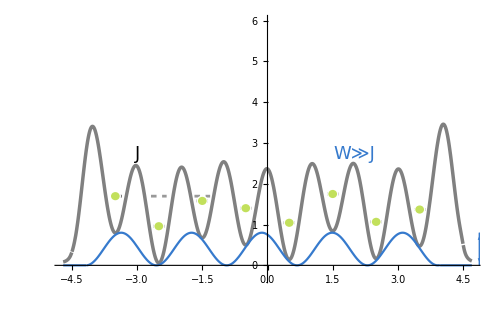
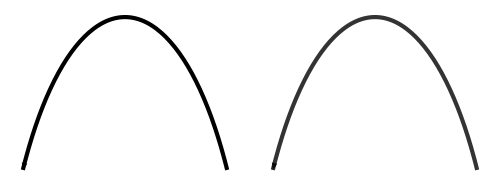

MBL_Latt_Combo_noU1.pdf

```mathematica
SpikeBallRed=ColorData[93,"ColorList"]⟦1⟧;
USpikeBall=Graphics[{SpikeBallRed,Opacity[0.52],EdgeForm[{Thickness[0.000001],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-0.5,0.95+DisordF[-0.5]+Uo},0.52,0.75]}}];




DisordF[x_]:=WD*Cos[π x(GR-1)+Phi]^2 

DisordF1D[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x,4.5,0.05]

barelattV2=Plot[{Gauss[x,-4.1,0.2]/2+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

QP=Plot[{( DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-4.7,4.7},
AxesStyle-> Opacity[0],
PlotStyle-> {{QPLC}}];

LevelList=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,0.95+DisordF[-3.5]},{-3.48 + LW,0.95+DisordF[-3.5]}}],
Line[{{-2.5 - LW,0.95+DisordF[-2.5]},{-2.5+ LW,0.95+DisordF[-2.5]}}],
Line[{{-1.5- LW,0.95+DisordF[-1.5]},{-1.5+ LW,0.95+DisordF[-1.5]}}],
Line[{{-0.5 - LW,0.95+DisordF[-0.5]},{-0.5+ LW,0.95+DisordF[-0.5]}}],
Line[{{0.5 - LW,0.95+DisordF[0.5]},{0.5 + LW,0.95+DisordF[0.5]}}],Line[{{1.5- LW,0.95+DisordF[1.5]},{1.5 + LW,0.95+DisordF[1.5]}}],
Line[{{2.5- LW,0.95+DisordF[2.5]},{2.5+ LW,0.95+DisordF[2.5]}}],
Line[{{3.5 - LW,0.95+DisordF[3.5]},{3.5+ LW,0.95+DisordF[3.5]}}]
}];




AtomListShadow2a=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-3.5,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomShdwR,atomShdwR}]}];
AtomListShadow2b=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-2.5+0.04,0.95+DisordF[-2.5]+Uo-0.03},{atomShdwR,atomShdwR}],
}];


AtomList2a=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-3.5,0.95+DisordF[-3.5]},{atomR,atomR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomR,atomR}]}];




DLevels= Graphics[{Thickness[0.004],
RGBColor["Black"],
Opacity[0.4],
Dashing[0.008],
Line[{{-1.5- LW3,0.95+DisordF[-3.5]},{-1.5+ LW3,0.95+DisordF[-3.5]}}],
Line[{{-2.5 - LW3,0.95+DisordF[-3.5]},{-2.5+ LW3,0.95+DisordF[-3.5]}}]
}];



ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[GrayLevel[0],Opacity[1],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.075,{0.2π,π 0.8}}};
arcsHop1 = Graphics[{
{Inset[arcsWArrows[rdsAndAngls],{-3,DisordF[-1.5]+1.3}]}
}];

ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[GrayLevel[0],Opacity[0.8],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.075,{0.2π,π 0.8}}};
arcsHop2 = Graphics[{
{Inset[arcsWArrows[rdsAndAngls],{-2,DisordF[-1.5]+1.3}]}
}];

EXPPlot=Plot[
Exp[-Abs[x+3]/0.5]+3,
{x,-4.5,4.5},
PlotRange-> {{-3.2,3.2},{-0.3,6}},
PlotStyle-> {RGBColor[{0,0,0}]},
AxesStyle-> Opacity[0]
];

labelsb={Graphics[{
{Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-3,2.5},{0,-1}]},
{QPLC,Text[Style[ToExpression["W \\gg J",TeXForm,HoldForm],FntSz],{2,2.5},{0,-1}]}
}]};

MBL=Show[barelattV2,
LevelList,DLevels,
arcsHop1,arcsHop2,
WArrows,
QP,
AtomListShadow2a,AtomList2a,
labelsb
]

Export["MBL_Latt_Combo_noU1.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

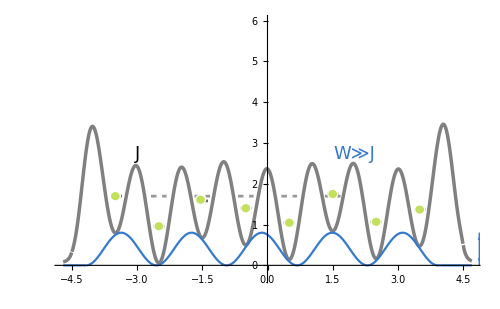
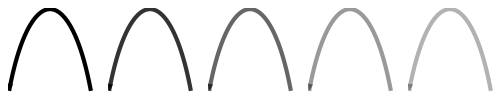

MBL_Latt_Combo_noU2.pdf

```mathematica
SpikeBallRed=ColorData[93,"ColorList"]⟦1⟧;
USpikeBall=Graphics[{SpikeBallRed,Opacity[0.52],EdgeForm[{Thickness[0.000001],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-0.5,0.95+DisordF[-0.5]+Uo},0.52,0.75]}}];

DisordF[x_]:=WD*Cos[π x(GR-1)+Phi]^2 

DisordF1D[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x,4.5,0.05]

barelattV2=Plot[{Gauss[x,-4.1,0.2]/2+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

QP=Plot[{( DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-4.7,4.7},
AxesStyle-> Opacity[0],
PlotStyle-> {{QPLC}}];

LevelList=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,0.95+DisordF[-3.5]},{-3.48 + LW,0.95+DisordF[-3.5]}}],
Line[{{-2.5 - LW,0.95+DisordF[-2.5]},{-2.5+ LW,0.95+DisordF[-2.5]}}],
Line[{{-1.5- LW,0.95+DisordF[-1.5]},{-1.5+ LW,0.95+DisordF[-1.5]}}],
Line[{{-0.5 - LW,0.95+DisordF[-0.5]},{-0.5+ LW,0.95+DisordF[-0.5]}}],
Line[{{0.5 - LW,0.95+DisordF[0.5]},{0.5 + LW,0.95+DisordF[0.5]}}],Line[{{1.5- LW,0.95+DisordF[1.5]},{1.5 + LW,0.95+DisordF[1.5]}}],
Line[{{2.5- LW,0.95+DisordF[2.5]},{2.5+ LW,0.95+DisordF[2.5]}}],
Line[{{3.5 - LW,0.95+DisordF[3.5]},{3.5+ LW,0.95+DisordF[3.5]}}]
}];

DLevels= Graphics[{Thickness[0.004],
RGBColor["Black"],
Opacity[0.4],
Dashing[0.008],
Line[{{-2.5- LW3,0.95+DisordF[-3.5]},{-2.5+ LW3,0.95+DisordF[-3.5]}}],
Line[{{-1.5 - LW3,0.95+DisordF[-3.5]},{-1.5+ LW3,0.95+DisordF[-3.5]}}],
Line[{{-0.5- LW3,0.95+DisordF[-3.5]},{-0.5+ LW3,0.95+DisordF[-3.5]}}],
Line[{{0.5 - LW3,0.95+DisordF[-3.5]},{0.5+ LW3,0.95+DisordF[-3.5]}}],
Line[{{1.5 - LW3,0.95+DisordF[-3.5]},{1.5+ LW3,0.95+DisordF[-3.5]}}]
}];


AtomListShadow2a=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-1.5-0.04,0.95+DisordF[-1.5]+Uo+0.03},{atomShdwR,atomShdwR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}],
Disk[{-3.5,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomShdwR,atomShdwR}]}];

AtomListShadow2b=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-1.5+0.04,0.95+DisordF[-1.5]+Uo-0.03},{atomShdwR,atomShdwR}],
}];


AtomList2a=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-1.5-0.04,0.95+DisordF[-1.5]+Uo+0.03},{atomR,atomR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}],
Disk[{-3.5,0.95+DisordF[-3.5]},{atomR,atomR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomR,atomR}]}];

AtomList2b=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-1.5+0.04,0.95+DisordF[-1.5]+Uo-0.03},{atomR,atomR}]
}];

labelsb={Graphics[{
{Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-3,2.5},{0,-1}]},
{QPLC,Text[Style[ToExpression["W \\gg J",TeXForm,HoldForm],FntSz],{2,2.5},{0,-1}]}
}]};

ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[GrayLevel[0],Opacity[0.6],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.075,{0.2π,π 0.8}}};
arcsHop3 = Graphics[{
{Inset[arcsWArrows[rdsAndAngls],{-1,DisordF[-1.5]+1.3}]}
}];


ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[GrayLevel[0],Opacity[0.4],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.075,{0.2π,π 0.8}}};
arcsHop4 = Graphics[{
{Inset[arcsWArrows[rdsAndAngls],{0,DisordF[-1.5]+1.3}]}
}];


ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[GrayLevel[0],Opacity[0.3],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.075,{0.2π,π 0.8}}};
arcsHop5 = Graphics[{
{Inset[arcsWArrows[rdsAndAngls],{1,DisordF[-1.5]+1.3}]}
}];


(*LevelList2,LevelList3*)
MBL=Show[barelattV2,
LevelList,DLevels,
arcsHop1,arcsHop2,arcsHop3,arcsHop4,arcsHop5,
WArrows,
QP,
AtomListShadow2a,AtomList2a,
labelsb]

Export["MBL_Latt_Combo_noU2.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

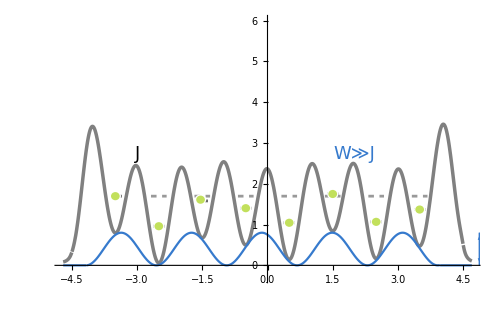
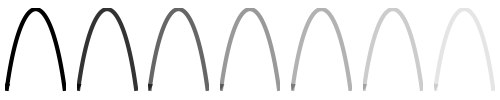

MBL_Latt_Combo_noU3.pdf

```mathematica
pikeBallRed=ColorData[93,"ColorList"]⟦1⟧;
USpikeBall=Graphics[{SpikeBallRed,Opacity[0.52],EdgeForm[{Thickness[0.000001],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-0.5,0.95+DisordF[-0.5]+Uo},0.52,0.75]}}];

DisordF[x_]:=WD*Cos[π x(GR-1)+Phi]^2 

DisordF1D[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x,4.5,0.05]

barelattV2=Plot[{Gauss[x,-4.1,0.2]/2+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

QP=Plot[{( DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-4.7,4.7},
AxesStyle-> Opacity[0],
PlotStyle-> {{QPLC}}];

LevelList=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,0.95+DisordF[-3.5]},{-3.48 + LW,0.95+DisordF[-3.5]}}],
Line[{{-2.5 - LW,0.95+DisordF[-2.5]},{-2.5+ LW,0.95+DisordF[-2.5]}}],
Line[{{-1.5- LW,0.95+DisordF[-1.5]},{-1.5+ LW,0.95+DisordF[-1.5]}}],
Line[{{-0.5 - LW,0.95+DisordF[-0.5]},{-0.5+ LW,0.95+DisordF[-0.5]}}],
Line[{{0.5 - LW,0.95+DisordF[0.5]},{0.5 + LW,0.95+DisordF[0.5]}}],Line[{{1.5- LW,0.95+DisordF[1.5]},{1.5 + LW,0.95+DisordF[1.5]}}],
Line[{{2.5- LW,0.95+DisordF[2.5]},{2.5+ LW,0.95+DisordF[2.5]}}],
Line[{{3.5 - LW,0.95+DisordF[3.5]},{3.5+ LW,0.95+DisordF[3.5]}}]
}];

DLevels= Graphics[{Thickness[0.004],
RGBColor["Black"],
Opacity[0.4],
Dashing[0.008],
Line[{{-2.5- LW3,0.95+DisordF[-3.5]},{-2.5+ LW3,0.95+DisordF[-3.5]}}],
Line[{{-1.5 - LW3,0.95+DisordF[-3.5]},{-1.5+ LW3,0.95+DisordF[-3.5]}}],
Line[{{-0.5- LW3,0.95+DisordF[-3.5]},{-0.5+ LW3,0.95+DisordF[-3.5]}}],
Line[{{0.5 - LW3,0.95+DisordF[-3.5]},{0.5+ LW3,0.95+DisordF[-3.5]}}],
Line[{{1.5 - LW3,0.95+DisordF[-3.5]},{1.5+ LW3,0.95+DisordF[-3.5]}}],
Line[{{2.5 - LW3,0.95+DisordF[-3.5]},{2.5+ LW3,0.95+DisordF[-3.5]}}],
Line[{{3.5 - LW3,0.95+DisordF[-3.5]},{3.5+ LW3,0.95+DisordF[-3.5]}}]
}];


AtomListShadow2a=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-1.5-0.04,0.95+DisordF[-1.5]+Uo+0.03},{atomShdwR,atomShdwR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}],
Disk[{-3.5,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomShdwR,atomShdwR}]}];

AtomListShadow2b=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{-1.5+0.04,0.95+DisordF[-1.5]+Uo-0.03},{atomShdwR,atomShdwR}],
}];


AtomList2a=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-1.5-0.04,0.95+DisordF[-1.5]+Uo+0.03},{atomR,atomR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}],
Disk[{-3.5,0.95+DisordF[-3.5]},{atomR,atomR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}],
Disk[{3.5,0.95+DisordF[3.5]},{atomR,atomR}]}];

AtomList2b=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{-1.5+0.04,0.95+DisordF[-1.5]+Uo-0.03},{atomR,atomR}]
}];

labelsb={Graphics[{
{Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-3,2.5},{0,-1}]},
{QPLC,Text[Style[ToExpression["W \\gg J",TeXForm,HoldForm],FntSz],{2,2.5},{0,-1}]}
}]};




ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[GrayLevel[0],Opacity[0.2],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.075,{0.2π,π 0.8}}};
arcsHop6 = Graphics[{
{Inset[arcsWArrows[rdsAndAngls],{2,DisordF[-1.5]+1.3}]}
}];


ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[GrayLevel[0],Opacity[0.1],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.075,{0.2π,π 0.8}}};
arcsHop7 = Graphics[{
{Inset[arcsWArrows[rdsAndAngls],{3,DisordF[-1.5]+1.3}]}
}];


(*LevelList2,LevelList3*)
MBL=Show[barelattV2,
LevelList,DLevels,
arcsHop1,arcsHop2,arcsHop3,arcsHop4,arcsHop5,arcsHop6,arcsHop7,
WArrows,
QP,
AtomListShadow2a,AtomList2a,
labelsb]

Export["MBL_Latt_Combo_noU3.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

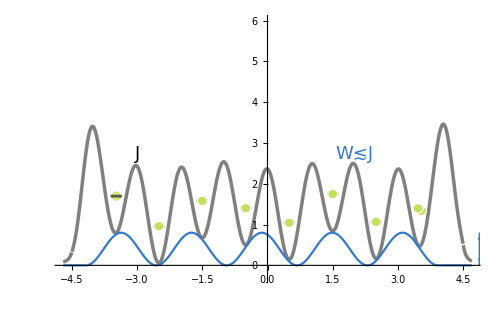
-Graphics-
-Graphics-

MBL_Latt_Combo_noU4.pdf

```mathematica
SpikeBallRed=ColorData[93,"ColorList"]⟦1⟧;
USpikeBall=Graphics[{SpikeBallRed,Opacity[0.52],EdgeForm[{Thickness[0.000001],Opacity[0.6]}],
FilledCurve@{GenerateSpikeBall[{-0.5,0.95+DisordF[-0.5]+Uo},0.52,0.75]}}];

DisordF[x_]:=WD*Cos[π x(GR-1)+Phi]^2 

DisordF1D[x_]:=((2-GR) WD Sin[π x (GR-1) +Phi- π/2]^2+(GR-1) WD Cos[π x (GR-2) +Phi -π/2]^2)SmoothBox[x,4.5,0.05]

barelattV2=Plot[{Gauss[x,-4.1,0.2]/2+2*Cos[π x]^2 If[x<4.5 && x>-4.5,1,0]+Gauss[x,4.1,0.2]/2+ DisordF1D[x]+0.05},
{x,-4.7,4.7},
PlotRange-> {{-4.7,4.7},{-0.3,6}},
PlotStyle-> {RGBColor["gray"],Thickness[0.005]},
AxesStyle-> Opacity[0],
ImageSize-> 500];

QP=Plot[{( DisordF[x]*If[x>(2 0.2 1.6 - 3 1.6) && x<(2 0.24 1.6 + 2 1.6),1,0])},
{x,-4.7,4.7},
AxesStyle-> Opacity[0],
PlotStyle-> {{QPLC}}];

LevelList=Graphics[{ Thickness[0.004],
RGBColor["Black"],
Opacity[0.6],
Line[{{-3.48 - LW,0.95+DisordF[-3.5]},{-3.48 + LW,0.95+DisordF[-3.5]}}],
Line[{{-2.5 - LW,0.95+DisordF[-2.5]},{-2.5+ LW,0.95+DisordF[-2.5]}}],
Line[{{-1.5- LW,0.95+DisordF[-1.5]},{-1.5+ LW,0.95+DisordF[-1.5]}}],
Line[{{-0.5 - LW,0.95+DisordF[-0.5]},{-0.5+ LW,0.95+DisordF[-0.5]}}],
Line[{{0.5 - LW,0.95+DisordF[0.5]},{0.5 + LW,0.95+DisordF[0.5]}}],Line[{{1.5- LW,0.95+DisordF[1.5]},{1.5 + LW,0.95+DisordF[1.5]}}],
Line[{{2.5- LW,0.95+DisordF[2.5]},{2.5+ LW,0.95+DisordF[2.5]}}],
Line[{{3.5 - LW,0.95+DisordF[3.5]},{3.5+ LW,0.95+DisordF[3.5]}}]
}];


AtomList2d=Graphics[{
diskgreen,
Opacity[0.55],
EdgeForm[Dashing[0.005]],
Disk[{-3.48,0.95+DisordF[-3.5]},{atomR,atomR}]}];

AtomListShadow2d=Graphics[{ 
RGBColor["White"],
Opacity[0.4],
Disk[{-3.48,0.95+DisordF[-3.5]},{atomShdwR,atomShdwR}]
}];

AtomListShadow2a=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{3.5-0.04,0.95+DisordF[3.5]+Uo+0.03},{atomShdwR,atomShdwR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomShdwR,atomShdwR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomShdwR,atomShdwR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomShdwR,atomShdwR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomShdwR,atomShdwR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomShdwR,atomShdwR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomShdwR,atomShdwR}]}];
AtomListShadow2b=Graphics[{ 
RGBColor["White"],
Opacity[1],
Disk[{3.5+0.04,0.95+DisordF[3.5]+Uo-0.03},{atomShdwR,atomShdwR}],
}];


AtomList2a=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{3.5-0.04,0.95+DisordF[3.5]+Uo+0.03},{atomR,atomR}],
Disk[{-1.5,0.95+DisordF[-1.5]},{atomR,atomR}],
Disk[{-2.5,0.95+DisordF[-2.5]},{atomR,atomR}],
Disk[{-0.5,0.95+DisordF[-0.5]},{atomR,atomR}],
Disk[{0.5,0.95+DisordF[0.5]},{atomR,atomR}],
Disk[{2.5,0.95+DisordF[2.5]},{atomR,atomR}],
Disk[{1.5,0.95+DisordF[1.5]},{atomR,atomR}]}];

AtomList2b=Graphics[{ 
diskgreen,
Opacity[0.8],
Disk[{3.5+0.04,0.95+DisordF[3.5]+Uo-0.03},{atomR,atomR}]
}];

labelsb={Graphics[{
{Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{-3,2.5},{0,-1}]},
{QPLC,Text[Style[ToExpression["W \\lesssim J",TeXForm,HoldForm],FntSz],{2,2.5},{0,-1}]}
}]};

ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Thickness[0.015],Directive[GrayLevel[0],
Arrowheads[{{-0.06,0},{0.06,1}}]
]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]

rdsAndAngls={{0.075,{0.2π,π 0.8}}};
arcsHop = Graphics[{
Inset[arcsWArrows[rdsAndAngls],{-3,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{-2,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{-1,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{0,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{1,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{2,DisordF[-1.5]+1.3}],
Inset[arcsWArrows[rdsAndAngls],{3,DisordF[-1.5]+1.3}]
}];

MBL=Show[barelattV2,
AtomListShadow2d,AtomList2d,
LevelList,
arcsHop,WArrows,
QP,
AtomListShadow2b,AtomList2b,
AtomListShadow2a,AtomList2a,
labelsb]

Export["MBL_Latt_Combo_noU4.pdf",%,ImageResolution-> 2000,Rasterize-> False]
```

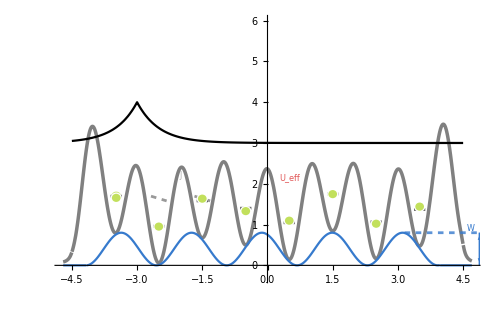
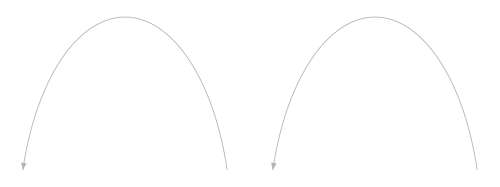

```mathematica
DLevels= Graphics[{Thickness[0.004],
RGBColor["Black"],
Opacity[0.4],
Dashing[0.008],
Line[{{-1.5- LW3,0.95+DisordF[-3.5]},{-1.5+ LW3,0.95+DisordF[-1.5]}}],
Line[{{-2.5 - LW3,0.95+DisordF[-3.5]},{-2.5+ LW3,0.95+DisordF[-1.5]}}]
}];
AL2=Show[barelattV2,
LevelList,WLevels,DLevels,
AtomList2d,arcsSS,WArrows,
(*GQP1,GQP2,GQP3,GQP4,GQP5,GQP6,GQP7,GQP8,*)
QP,
(*AtomListShadow,AtomList,*)
AtomListShadow,AtomList,
labelsa,
EXPPlot]
```